## VE401 RC 2

## Continuous Random Variables

#### Exponential Distribution

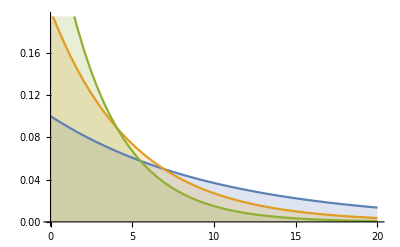

```mathematica
Plot[Table[PDF[ExponentialDistribution[β], x], {β, {0.1, 0.2, 0.3}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Gamma Distribution

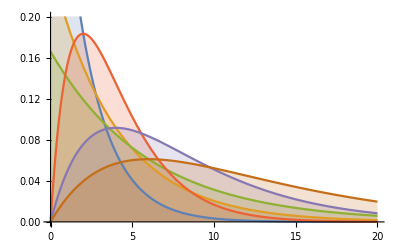

```mathematica
Plot[Table[PDF[GammaDistribution[α, β], x], {α, {1, 2}}, {β, {2, 4, 6}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Chi-Squared Distribution

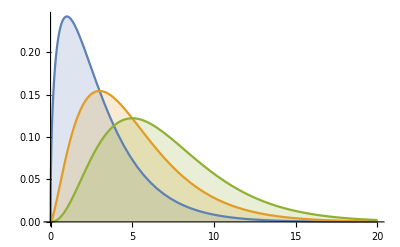

```mathematica
Plot[Table[PDF[ChiSquareDistribution[γ], x], {γ, {3, 5, 7}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Normal Distribution

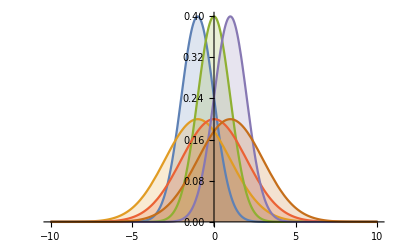

```mathematica
Plot[Table[PDF[NormalDistribution[μ, σ], x], {μ, {-1, 0, 1}}, {σ, {1, 2}}] // Evaluate, {x, -10, 10}, Filling->Axis]
```

## VE401 RC 4

## Statistical Distributions

### Standard Normal Distribution

```mathematica
InverseCDF[NormalDistribution[0, 1], 0.95]
```

1.64485

```mathematica
InverseCDF[NormalDistribution[0, 1], 0.975]
```

1.95996

### Chi-squared Distribution

```mathematica
InverseCDF[ChiSquareDistribution[10], 0.95]
```

18.307

### T Distribution

```mathematica
InverseCDF[StudentTDistribution[10], 0.95]
```

1.81246

## Case Study

```mathematica
X = Round[RandomVariate[NormalDistribution[4.5, 2], 70], 0.01]
n = 70
```

{1.67,3.6,2.67,11.3,3.86,2.67,4.43,5.86,3.12,2.86,7.24,3.31,4.98,6.68,3.27,6.32,3.94,4.14,4.9,1.98,7.27,5.84,1.33,7.86,4.12,2.39,9.,5.03,6.03,7.85,1.94,3.52,5.49,6.57,8.9,7.73,5.18,4.3,7.37,5.02,6.82,1.24,3.66,0.94,2.22,5.37,3.13,2.44,3.43,3.89,4.53,1.37,4.88,3.15,1.63,0.62,3.49,3.06,2.76,5.47,3.26,5.77,6.64,5.74,2.19,1.42,3.82,2.76,2.29,6.93}

```mathematica
X={1.67,3.6,2.67,11.3,3.86,2.67,4.43,5.86,3.12,2.86,7.24,3.31,4.98,6.68,3.27,6.32,3.94,4.14,4.9,1.98,7.2700000000000005,5.84,1.33,7.86,4.12,2.39,9.,5.03,6.03,7.8500000000000005,1.94,3.52,5.49,6.57,8.9,7.73,5.18,4.3,7.37,5.0200000000000005,6.82,1.24,3.66,0.9400000000000001,2.22,5.37,3.13,2.44,3.43,3.89,4.53,1.37,4.88,3.15,1.6300000000000001,0.62,3.49,3.06,2.7600000000000002,5.47,3.2600000000000002,5.7700000000000005,6.640000000000001,5.74,2.19,1.42,3.8200000000000003,2.7600000000000002,2.29,6.93}
```

{1.67,3.6,2.67,11.3,3.86,2.67,4.43,5.86,3.12,2.86,7.24,3.31,4.98,6.68,3.27,6.32,3.94,4.14,4.9,1.98,7.27,5.84,1.33,7.86,4.12,2.39,9.,5.03,6.03,7.85,1.94,3.52,5.49,6.57,8.9,7.73,5.18,4.3,7.37,5.02,6.82,1.24,3.66,0.94,2.22,5.37,3.13,2.44,3.43,3.89,4.53,1.37,4.88,3.15,1.63,0.62,3.49,3.06,2.76,5.47,3.26,5.77,6.64,5.74,2.19,1.42,3.82,2.76,2.29,6.93}

```mathematica
n=Length[X]
```

70

```mathematica
{q1, q2, q3} = Quartiles[X]
iqr = InterquartileRange[X]
h = 2iqr / 70^(1/3)
Min[X]-0.005
Select[X, 1.5+0.615≥ #≥0.615&]
```

{2.76,3.915,5.84}

3.08

1.49468

0.615

{1.67,1.98,1.33,1.94,1.24,0.94,1.37,1.63,0.62,1.42}

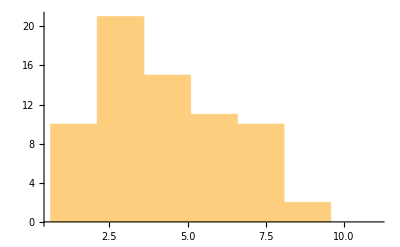

```mathematica
Histogram[X, {Min[X]-0.005, Max[X], h}]
```

```mathematica
Needs["StatisticalPlots`"]
StemLeafPlot[Floor[X, 0.1], IncludeEmptyStems->True]
```

Stem | Leaves
0 | 69
1 | 23346699
2 | 1223466778
3 | 0111223445668889
4 | 11245899
5 | 0013447788
6 | 0356689
7 | 223788
8 | 9
9 | 0
10 | 
11 | 3
Stem units: 1

```mathematica
f1 = q1 - 3/2*iqr
f3 = q3 + 3/2 *iqr
F1 = q1 - 3iqr
F3 = q3 + 3iqr
a1 = Min[Select[X, #≥f1&]]
a3 = Max[Select[X, #≤f3&]]
```

-1.86

10.46

-6.48

15.08

0.62

9.

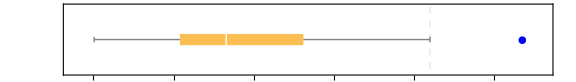

```mathematica
BoxWhiskerChart[
X, {"Outliers", {"Outliers",Blue},{"FarOutliers",Red}},
AspectRatio->1/7, BarOrigin->Left,
GridLines->{{{a3,Dashed},{F3,Dashed}},None},ImageSize->Large,FrameTicks->{
{None,None},
{Range[Min[Floor[X,0.1]],Max[Ceiling[X,0.1]]],
{{q1,"q1"},{q2,"q2"},{q3,"q3"},{a3,"near"},{F3,"far"}}}}
]
```

```mathematica
Mean[X]
Variance[X]
```

4.378

4.89576

```mathematica
z = InverseCDF[NormalDistribution[0, 1], 0.975]
Mean[X]-2z/Sqrt[70]
Mean[X]+2z/Sqrt[70]
```

1.95996

3.90948

4.84652

```mathematica
c1 = InverseCDF[ChiSquareDistribution[69], 0.025]
c2 = InverseCDF[ChiSquareDistribution[69], 0.975]
(n-1)Variance[X]/c2
(n-1)Variance[X]/c1
```

47.9242

93.8565

3.59919

7.04879

```mathematica
t = InverseCDF[StudentTDistribution[69], 0.975]
Mean[X] - t Variance[X]/Sqrt[n]
Mean[X] + t Variance[X]/Sqrt[n]
```

1.99495

3.21065

5.54535

{188.12,193.71,193.73,195.45,200.81,201.63,202.2,202.21,203.62,204.55,208.15,211.14,219.54,221.31,224.39,226.16}

{198.13,202.915,215.34}

17.21

172.315

241.155

146.5

266.97

188.12

226.16

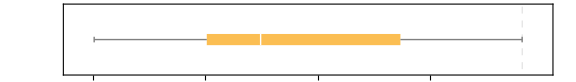

```mathematica
(*** For QA ***)
X = {188.12, 193.71, 193.73, 195.45, 200.81, 201.63, 202.2, 202.21, 203.62, 204.55, 208.15, 211.14, 219.54, 221.31, 224.39, 226.16}
{q1, q2, q3} = Quartiles[X]
iqr = InterquartileRange[X]
f1 = q1 - 3/2*iqr
f3 = q3 + 3/2 *iqr
F1 = q1 - 3iqr
F3 = q3 + 3iqr
a1 = Min[Select[X, #≥f1&]]
a3 = Max[Select[X, #≤f3&]]
BoxWhiskerChart[
X, {"Outliers", {"Outliers",Blue},{"FarOutliers",Red}},
AspectRatio->1/7, BarOrigin->Left,
GridLines->{{{a3,Dashed},{F3,Dashed}},None},ImageSize->Large,FrameTicks->{
{None,None},
{Range[Min[Floor[X,1]],Max[Ceiling[X,1]], 10],
{{q1,"q1"},{q2,"q2"},{q3,"q3"},{a3,"near"},{F3,"far"}}}}
]
```

```mathematica
(*** Lec 11 ***)
data = {79,141,228,3,20,14,97,194,28,56,75,37,122,27,10,67,23,20,103,11,92,99,64,6,118,136,682,4,70,11,74,40,16,114,8,149,97,7,317,346,188,149,68,150,88,87,155,50,26,143,126,98,153,238,30,53,132,260,296,25,61,87,33,51,74,111,72,178,4,67,43,229,156,117,104,27,23,23,186,524,107,160,41,50,352,8,153,142,306,320,85,44,116,39,264,360,192,142,44,29}
n=Length[data]
```

{79,141,228,3,20,14,97,194,28,56,75,37,122,27,10,67,23,20,103,11,92,99,64,6,118,136,682,4,70,11,74,40,16,114,8,149,97,7,317,346,188,149,68,150,88,87,155,50,26,143,126,98,153,238,30,53,132,260,296,25,61,87,33,51,74,111,72,178,4,67,43,229,156,117,104,27,23,23,186,524,107,160,41,50,352,8,153,142,306,320,85,44,116,39,264,360,192,142,44,29}

100

```mathematica
{q1, q2, q3} = Quartiles[data]
iqr = InterquartileRange[data]
h = 2iqr/n^(1/3)
m1 = Min[data]-0.5
m2 = Max[data]
```

{35,87,299/2}

229/2

229/10^(2/3)

2.5

682

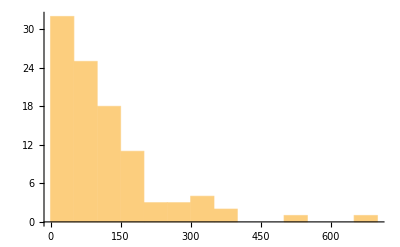

```mathematica
Histogram[data, "FreedmanDiaconis"]
```

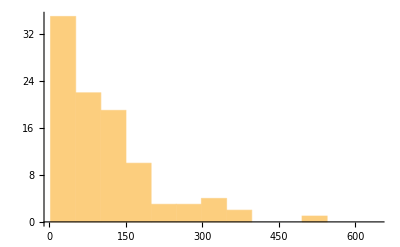

```mathematica
Histogram[data,{m1, m2, h}]
```

{7.78,5.5,6.2,6.08,7.35,6.71,6.19,8.26,8.26,7.47,7.37,4.62,7.96,7.36,7.24,7.05,6.4,4.02,7.72,6.91,6.45,6.52,8.57,5.56,8.71,6.6,6.71,6.64,6.67,7.54,7.66,6.59,7.97,7.61,7.28,7.5,7.55,7.5,7.62,6.87,5.25,5.71,5.99,7.91,7.36,5.75,7.18,7.11,6.8,5.6,6.6,6.46,7.6,7.,7.54,5.6,6.25,8.02,6.59,7.76,7.97,6.22,7.43,6.68,6.69,8.71,7.91,6.86,5.53,7.95}

{6.45,7.025,7.61}

1.16

0.57

4.015

9.145

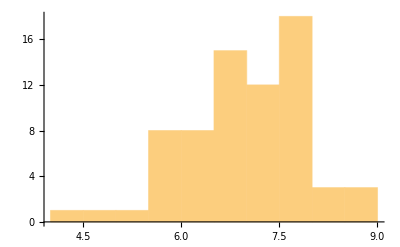

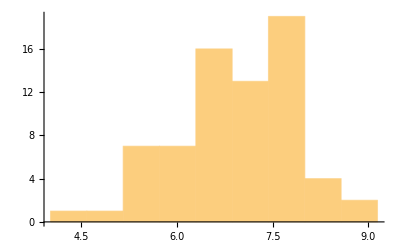

```mathematica
(*** test ***)
n = 70;
precision = 0.01;
data = Round[RandomVariate[NormalDistribution[7, 1], n], precision]
{q1, q2, q3} = Quartiles[data]
iqr = InterquartileRange[data]
h = Ceiling[2iqr/n^(1/3),precision]
l = Min[data]-precision/2
u = Ceiling[(Max[data]-l)/h,1]*h+l
Histogram[data, "FreedmanDiaconis"]
Histogram[data,{l, u, h}]
```

## Assignment 4

### Ex. 4.1

Stem | Leaves | Counts
532 | 9 | 1
533 |  | 0
534 | 2 | 1
535 | 47 | 2
536 | 6 | 1
537 | 5678 | 4
538 | 12345778888 | 11
539 | 016999 | 6
540 | 11166677889 | 11
541 | 123666688 | 9
542 | 0011222357899 | 13
543 | 01111556 | 8
544 | 00012455678 | 11
545 | 233447899 | 9
546 | 23569 | 5
547 | 357 | 3
548 | 11257 | 5
Stem units: 10

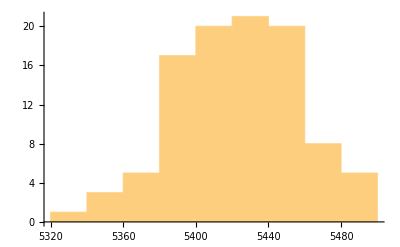

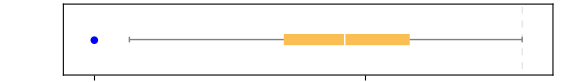

```mathematica
X = {5408,5431,5475,5442,5376,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5457,5407,5469,5416,5377,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5444,5466,5399,5391,5477,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5427,5421,5396,5381,5425,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5406,5342,5452,5420,5458,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440,5422,5448,5366,5430,5418};
Needs["StatisticalPlots`"]
StemLeafPlot[X, IncludeEmptyStems->True,IncludeStemCounts->True,StemExponent->{1,"UnitDivisions"->1}]
Histogram[X, "FreedmanDiaconis"]
{q1, q2, q3} = Quartiles[X];
iqr = InterquartileRange[X];
f1 = q1 - 3/2*iqr;
f3 = q3 + 3/2 *iqr;
F1 = q1 - 3iqr;
F3 = q3 + 3iqr;
a1 = Min[Select[X, #≥f1&]];
a3 = Max[Select[X, #≤f3&]];
BoxWhiskerChart[
X, {"Outliers", {"Outliers",Blue},{"FarOutliers",Red}},
AspectRatio->1/7, BarOrigin->Left,
GridLines->{{{a3,Dashed},{F3,Dashed}},None},ImageSize->Large,FrameTicks->{
{None,None},
{Range[Min[Floor[X,1]],Max[Ceiling[X,1]], 100],
{{q1,"q1"},{q2,"q2"},{q3,"q3"},{a3,"near"},{F3,"far"}}}}
]
```

## VE401 RC 5

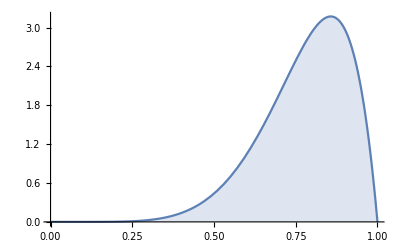

```mathematica
Plot[PDF[BetaDistribution[7, 2], x], {x, 0, 1}, Filling->Axis]
```

```mathematica
p=CDF[BetaDistribution[7,2],0.5]
(1-p)/p
```

0.0351563

27.4444

```mathematica
data={41.50,41.38,42.24,41.85,41.76,42.08,41.62,42.16,41.71,41.44};
Needs["HypothesisTesting`"]
FisherRatioTest[data,0.1,"TestDataTable",AlternativeHypothesis->"Unequal"]
```

| Statistic | P-Value
Fisher Ratio | 8.3544 | 0.997726

```mathematica
1-CDF[ChiSquareDistribution[19],29.503]
```

0.0584741

```mathematica
data = {5,1,5,4,4,6,6,3,6,2,3,5,5,6,4,4,4,3,3,4};
m0=3;
Qp=Length[Select[data, #>m0&]] (* Q+ *)
Qm=Length[Select[data, #<m0&]] (* Q- *)
n=Qp+Qm;
SignTest[data,m0,"TestDataTable",AlternativeHypothesis->"Greater"]
CDF[BinomialDistribution[n,0.5],Qp]
CDF[BinomialDistribution[n,0.5],Qm]
```

14

2

| Statistic | P-Value
Sign | 14 | 0.00209045

0.999741

0.00209045

```mathematica
data={1,2,3,3,3,3,4,4,4,4,4,4,5,5,5,5,6,6,6,6};
m0=3.5;
SignedRankTest[data,m0,"TestDataTable",AlternativeHypothesis->"Greater"]
```

| Statistic | P-Value
Signed-Rank | 157. | 0.0251201

## Exercise 1.

```mathematica
n=12;
data=Round[RandomVariate[NormalDistribution[2.7, 1], n],0.01]
```

{1.85,3.53,3.22,3.11,3.78,2.81,4.16,3.32,4.01,2.5,4.,2.95}

```mathematica
n1=16;
X1={2.55,2.11,2.76,2.19,2.94,2.41,2.27,1.98,2.72,2.26,2.65,2.68,2.15,2.33,2.32,1.88};
n2=12;
X2={2.85,2.73,2.92,2.11,1.78,2.01,2.16,2.32,2.51,2.53,2.67,2.75};
(* mean *)
t1=InverseCDF[StudentTDistribution[n1-1],0.975]
T1=(Mean[X1]-2.30)/(StandardDeviation[X1]/Sqrt[n1])
Mean[X1]-t1*StandardDeviation[X1]/Sqrt[n1]
Mean[X1]+t1*StandardDeviation[X1]/Sqrt[n1]
0.2/StandardDeviation[X1]
(* variance *)
c1=InverseCDF[ChiSquareDistribution[n1-1],0.05]
C1=(n1-1)StandardDeviation[X1]^2/0.5^2
(n1-1)StandardDeviation[X1]^2/c1^2
StandardDeviation[X1]/0.5
(* sign test *)
m0=2.5;
qp=Length[Select[X1,#>m0&]]
qm=Length[Select[X1,#<m0&]]
SignTest[X1,m0,"TestDataTable",AlternativeHypothesis->"Unequal"]
CDF[BinomialDistribution[n1,0.5],qp]
CDF[BinomialDistribution[n1,0.5],qm]
(* signed rank test *)
m0=2.5;
order=Ordering[Abs[X1-m0]];
X1[[order]]
Sort[Abs[X1-m0]]
1+3+5+7+10+14
-2-4-6-8-9-11-12-13-15-16
mean=N[n1(n1+1)/4]
stddev=N[Sqrt[n1(n1+1)(2n1+1)/24]]
InverseCDF[NormalDistribution[0,1],0.975]
(96-mean)/stddev
(* test proportion *)
p0=0.5;
p1=Length[Select[X1,2.3+0.4># &&2.3-0.4<#&]]/n1
(p1-p0)/Sqrt[p0(1-p0)/n1]
InverseCDF[NormalDistribution[0,1],0.95]
(* compare proportions *)
p2=N[Length[Select[X2,2.3+0.4># &&2.3-0.4<#&]]/n2]
p=N[(n1*p1+n2*p2)/(n1+n2)]
(p1-p2)/Sqrt[p(1-p)(1/n1+1/n2)]
InverseCDF[NormalDistribution[0,1],0.975]
(* compare variances *)
s1=StandardDeviation[X1]
s2=StandardDeviation[X2]
s1^2
s2^2
f1=(s1/s2)^2
f2=(s2/s1)^2
InverseCDF[FRatioDistribution[n1-1,n2-1],0.975]
InverseCDF[FRatioDistribution[n2-1,n1-1],0.975]
```

2.13145

1.15816

2.22647

2.54853

0.661807

7.26094

5.4796

0.0259838

0.604406

6

10

| Statistic | P-Value
Sign | 6 | 0.454498

0.227249

0.894943

{2.55,2.41,2.65,2.33,2.68,2.32,2.72,2.27,2.26,2.76,2.19,2.15,2.11,2.94,1.98,1.88}

{0.05,0.09,0.15,0.17,0.18,0.18,0.22,0.23,0.24,0.26,0.31,0.35,0.39,0.44,0.52,0.62}

40

-96

68.

19.3391

1.95996

1.44785

3/4

2.

1.64485

0.583333

0.678571

0.934502

1.95996

0.302203

0.365128

0.0913267

0.133318

0.685028

1.45979

3.32993

3.00783

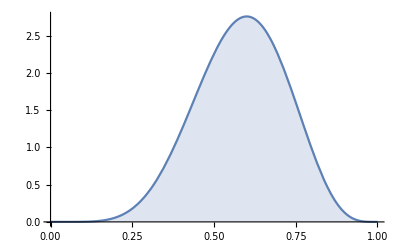

```mathematica
Plot[PDF[BetaDistribution[7, 5], x], {x, 0, 1}, Filling->Axis]
```

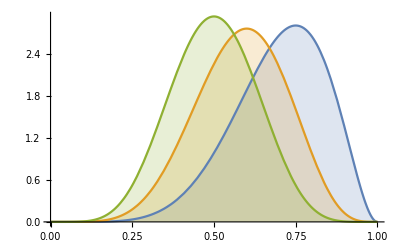

```mathematica
Plot[Table[PDF[BetaDistribution[7,b], x], {b, {3, 5, 7}}] // Evaluate, {x, 0, 1}, Filling->Axis]
```

## VE401 RC6

## Exercise 1.

```mathematica
n=20;
X1=Round[RandomVariate[NormalDistribution[2.7, 1], n],0.01]
X2=Round[RandomVariate[NormalDistribution[2.5, 1], n],0.01]
```

{2.81,3.32,3.01,2.74,2.78,0.53,1.92,3.12,1.97,1.58,2.65,2.62,2.92,3.13,3.75,3.62,4.35,2.04,3.65,2.57}

{1.56,2.08,0.35,3.45,1.41,3.83,2.42,2.34,4.01,4.36,3.96,3.69,2.87,3.31,3.01,0.86,1.96,3.42,3.67,2.02}

```mathematica
n=20;
X1={3.73,2.9,2.58,3.33,3.34,2.8,3.84,3.01,2.91,0.83,4.54,3.49,1.12,0.78,0.67,2.32,2.42,3.21,3.09,1.16};
X2={1.3,2.55,3.03,1.71,2.45,1.58,2.68,1.07,2.45,2.72,2.54,2.59,2.35,2.42,2.87,4.13,1.73,2.42,3.03,1.23};
```

```mathematica
m1=Mean[X1]
m2=Mean[X2]
```

2.6035

2.3425

```mathematica
(m1-m2)/Sqrt[1/10]
```

0.825354

```mathematica
InverseCDF[NormalDistribution[0,1],0.975]
```

1.95996

```mathematica
var1=Variance[X1]
var2=Variance[X2]
varp=(var1+var2)/2
```

1.26328

0.53442

0.898848

```mathematica
(m1-m2)/Sqrt[2varp/n]
```

0.870557

```mathematica
InverseCDF[StudentTDistribution[38],0.975]
```

2.02439

```mathematica
0.5/(2Sqrt[varp])
```

0.263692

```mathematica
(var1/n+var2/n)^2/((var1/n)^2/(n-1)+(var2/n)^2/(n-1))
```

32.6354

```mathematica
(m1-m2)/Sqrt[var1/n+var2/n]
```

0.870557

```mathematica
InverseCDF[StudentTDistribution[32],0.975]
```

2.03693

## Exercise 2.

```mathematica
p=N[(42+72+15+4)/(12*100)]
```

0.110833

```mathematica
p1=Binomial[12,0]*(1-p)^(12)
p2=Binomial[12,1]*p(1-p)^(11)
p3=Binomial[12,2]*p^2(1-p)^(10)
p4=Binomial[12,3]*p^3(1-p)^(9)
p5=1-Binomial[12,0]*(1-p)^(12)-Binomial[12,1]*p(1-p)^(11)-Binomial[12,2]*p^2(1-p)^(10)-Binomial[12,3]*p^3(1-p)^(9)
```

0.244229

0.365314

0.250447

0.10406

0.0359493

```mathematica
p5*100
```

3.59493

```mathematica
n=100;
(16-n*p1)^2/(n*p1)+(42-n*p2)^2/(n*p2)+(36-n*p3)^2/(n*p3)+(5-n*p4)^2/(n*p4)+(1-n*p5)^2/(n*p5)
```

13.1972

```mathematica
InverseCDF[ChiSquareDistribution[3],0.95]
```

7.81473

## VE401 Final

## PDF Table for F-distributions

```mathematica
n=20;
TableForm[Table[InverseCDF[FRatioDistribution[γ1,γ2],x],{γ1,Range[1,n,1]},{x,{0.005,0.010,0.025,0.05,0.10,0.25,0.50,0.75,0.90,0.95,0.975,0.99,0.995}},{γ2,Range[1,n,1]}],TableHeadings->{Range[1,n,1],{0.005,0.010,0.025,0.05,0.10,0.25,0.50,0.75,0.90,0.95,0.975,0.99,0.995},Range[1,n,1]}]//Style[#,PrintPrecision->4,FontFamily->"Latin Modern Sans",FontSize->10]&
```

| 0.005 | 0.01 | 0.025 | 0.05 | 0.1 | 0.25 | 0.5 | 0.75 | 0.9 | 0.95 | 0.975 | 0.99 | 0.995
1 | 1 | 0.0000616876
2 | 0.0000500013
3 | 0.0000462647
4 | 0.0000444453
5 | 0.000043373
6 | 0.0000426674
7 | 0.0000421682
8 | 0.0000417966
9 | 0.0000415093
10 | 0.0000412805
11 | 0.0000410942
12 | 0.0000409394
13 | 0.0000408088
14 | 0.0000406971
15 | 0.0000406006
16 | 0.0000405162
17 | 0.000040442
18 | 0.000040376
19 | 0.0000403171
20 | 0.0000402642 | 1 | 0.000246781
2 | 0.00020002
3 | 0.00018507
4 | 0.000177791
5 | 0.000173501
6 | 0.000170678
7 | 0.000168681
8 | 0.000167194
9 | 0.000166045
10 | 0.00016513
11 | 0.000164384
12 | 0.000163765
13 | 0.000163242
14 | 0.000162796
15 | 0.000162409
16 | 0.000162072
17 | 0.000161775
18 | 0.000161511
19 | 0.000161275
20 | 0.000161064 | 1 | 0.00154371
2 | 0.00125078
3 | 0.00115719
4 | 0.00111163
5 | 0.00108478
6 | 0.00106711
7 | 0.00105461
8 | 0.00104531
9 | 0.00103811
10 | 0.00103239
11 | 0.00102772
12 | 0.00102385
13 | 0.00102058
14 | 0.00101778
15 | 0.00101537
16 | 0.00101325
17 | 0.0010114
18 | 0.00100975
19 | 0.00100827
20 | 0.00100695 | 1 | 0.00619396
2 | 0.00501253
3 | 0.00463591
4 | 0.00445269
5 | 0.00434477
6 | 0.00427376
7 | 0.00422354
8 | 0.00418616
9 | 0.00415726
10 | 0.00413425
11 | 0.00411551
12 | 0.00409994
13 | 0.00408681
14 | 0.00407558
15 | 0.00406587
16 | 0.00405739
17 | 0.00404992
18 | 0.00404329
19 | 0.00403737
20 | 0.00403205 | 1 | 0.0250856
2 | 0.020202
3 | 0.0186591
4 | 0.0179106
5 | 0.0174703
6 | 0.0171808
7 | 0.0169762
8 | 0.016824
9 | 0.0167063
10 | 0.0166127
11 | 0.0165364
12 | 0.0164731
13 | 0.0164196
14 | 0.0163739
15 | 0.0163344
16 | 0.0162999
17 | 0.0162696
18 | 0.0162426
19 | 0.0162185
20 | 0.0161969 | 1 | 0.171573
2 | 0.133333
3 | 0.121953
4 | 0.116537
5 | 0.113381
6 | 0.111318
7 | 0.109865
8 | 0.108787
9 | 0.107955
10 | 0.107294
11 | 0.106757
12 | 0.106311
13 | 0.105935
14 | 0.105613
15 | 0.105336
16 | 0.105094
17 | 0.10488
18 | 0.104691
19 | 0.104522
20 | 0.10437 | 1 | 1.
2 | 0.666667
3 | 0.58506
4 | 0.548632
5 | 0.528074
6 | 0.51489
7 | 0.505723
8 | 0.498982
9 | 0.493818
10 | 0.489737
11 | 0.48643
12 | 0.483696
13 | 0.481399
14 | 0.479441
15 | 0.477753
16 | 0.476283
17 | 0.47499
18 | 0.473845
19 | 0.472823
20 | 0.471906 | 1 | 5.82843
2 | 2.57143
3 | 2.02386
4 | 1.8074
5 | 1.69247
6 | 1.62142
7 | 1.57322
8 | 1.53839
9 | 1.51206
10 | 1.49146
11 | 1.47491
12 | 1.46132
13 | 1.44997
14 | 1.44034
15 | 1.43207
16 | 1.42488
17 | 1.41859
18 | 1.41303
19 | 1.40809
20 | 1.40366 | 1 | 39.8635
2 | 8.52632
3 | 5.53832
4 | 4.54477
5 | 4.06042
6 | 3.77595
7 | 3.58943
8 | 3.45792
9 | 3.3603
10 | 3.28502
11 | 3.2252
12 | 3.17655
13 | 3.13621
14 | 3.10221
15 | 3.07319
16 | 3.04811
17 | 3.02623
18 | 3.00698
19 | 2.9899
20 | 2.97465 | 1 | 161.448
2 | 18.5128
3 | 10.128
4 | 7.70865
5 | 6.60789
6 | 5.98738
7 | 5.59145
8 | 5.31766
9 | 5.11736
10 | 4.9646
11 | 4.84434
12 | 4.74723
13 | 4.66719
14 | 4.60011
15 | 4.54308
16 | 4.494
17 | 4.45132
18 | 4.41387
19 | 4.38075
20 | 4.35124 | 1 | 647.789
2 | 38.5063
3 | 17.4434
4 | 12.2179
5 | 10.007
6 | 8.8131
7 | 8.07267
8 | 7.57088
9 | 7.20928
10 | 6.93673
11 | 6.72413
12 | 6.55377
13 | 6.41425
14 | 6.29794
15 | 6.1995
16 | 6.11513
17 | 6.04201
18 | 5.97805
19 | 5.92163
20 | 5.87149 | 1 | 4052.18
2 | 98.5025
3 | 34.1162
4 | 21.1977
5 | 16.2582
6 | 13.745
7 | 12.2464
8 | 11.2586
9 | 10.5614
10 | 10.0443
11 | 9.64603
12 | 9.33021
13 | 9.07381
14 | 8.86159
15 | 8.68312
16 | 8.53097
17 | 8.39974
18 | 8.28542
19 | 8.18495
20 | 8.09596 | 1 | 16210.7
2 | 198.501
3 | 55.552
4 | 31.3328
5 | 22.7848
6 | 18.635
7 | 16.2356
8 | 14.6882
9 | 13.6136
10 | 12.8265
11 | 12.2263
12 | 11.7542
13 | 11.3735
14 | 11.0603
15 | 10.798
16 | 10.5755
17 | 10.3842
18 | 10.2181
19 | 10.0725
20 | 9.94393
2 | 1 | 0.00503775
2 | 0.00502513
3 | 0.00502093
4 | 0.00501883
5 | 0.00501757
6 | 0.00501673
7 | 0.00501613
8 | 0.00501568
9 | 0.00501533
10 | 0.00501506
11 | 0.00501483
12 | 0.00501464
13 | 0.00501448
14 | 0.00501434
15 | 0.00501422
16 | 0.00501411
17 | 0.00501402
18 | 0.00501394
19 | 0.00501386
20 | 0.0050138 | 1 | 0.010152
2 | 0.010101
3 | 0.0100841
4 | 0.0100756
5 | 0.0100706
6 | 0.0100672
7 | 0.0100648
8 | 0.010063
9 | 0.0100616
10 | 0.0100604
11 | 0.0100595
12 | 0.0100588
13 | 0.0100581
14 | 0.0100576
15 | 0.0100571
16 | 0.0100567
17 | 0.0100563
18 | 0.0100559
19 | 0.0100557
20 | 0.0100554 | 1 | 0.0259698
2 | 0.025641
3 | 0.0255327
4 | 0.0254787
5 | 0.0254464
6 | 0.0254249
7 | 0.0254096
8 | 0.0253981
9 | 0.0253892
10 | 0.025382
11 | 0.0253762
12 | 0.0253713
13 | 0.0253672
14 | 0.0253636
15 | 0.0253606
16 | 0.0253579
17 | 0.0253556
18 | 0.0253535
19 | 0.0253516
20 | 0.0253499 | 1 | 0.0540166
2 | 0.0526316
3 | 0.0521804
4 | 0.0519567
5 | 0.0518231
6 | 0.0517343
7 | 0.051671
8 | 0.0516236
9 | 0.0515867
10 | 0.0515573
11 | 0.0515332
12 | 0.0515132
13 | 0.0514962
14 | 0.0514817
15 | 0.0514691
16 | 0.0514581
17 | 0.0514484
18 | 0.0514397
19 | 0.051432
20 | 0.0514251 | 1 | 0.117284
2 | 0.111111
3 | 0.109149
4 | 0.108185
5 | 0.107612
6 | 0.107233
7 | 0.106962
8 | 0.10676
9 | 0.106604
10 | 0.106478
11 | 0.106376
12 | 0.106291
13 | 0.106219
14 | 0.106157
15 | 0.106104
16 | 0.106057
17 | 0.106016
18 | 0.10598
19 | 0.105947
20 | 0.105918 | 1 | 0.388889
2 | 0.333333
3 | 0.317121
4 | 0.309401
5 | 0.304888
6 | 0.301927
7 | 0.299836
8 | 0.29828
9 | 0.297077
10 | 0.296119
11 | 0.295339
12 | 0.29469
13 | 0.294143
14 | 0.293675
15 | 0.293271
16 | 0.292917
17 | 0.292606
18 | 0.292329
19 | 0.292082
20 | 0.29186 | 1 | 1.5
2 | 1.
3 | 0.881102
4 | 0.828427
5 | 0.79877
6 | 0.779763
7 | 0.766548
8 | 0.756828
9 | 0.749381
10 | 0.743492
11 | 0.738719
12 | 0.734772
13 | 0.731455
14 | 0.728627
15 | 0.726187
16 | 0.724062
17 | 0.722193
18 | 0.720538
19 | 0.719061
20 | 0.717735 | 1 | 7.5
2 | 3.
3 | 2.27976
4 | 2.
5 | 1.85275
6 | 1.7622
7 | 1.70098
8 | 1.65685
9 | 1.62356
10 | 1.59754
11 | 1.57666
12 | 1.55953
13 | 1.54522
14 | 1.5331
15 | 1.52269
16 | 1.51366
17 | 1.50575
18 | 1.49876
19 | 1.49255
20 | 1.48698 | 1 | 49.5
2 | 9.
3 | 5.46238
4 | 4.32456
5 | 3.77972
6 | 3.4633
7 | 3.25744
8 | 3.11312
9 | 3.00645
10 | 2.92447
11 | 2.85951
12 | 2.8068
13 | 2.76317
14 | 2.72647
15 | 2.69517
16 | 2.66817
17 | 2.64464
18 | 2.62395
19 | 2.60561
20 | 2.58925 | 1 | 199.5
2 | 19.
3 | 9.55209
4 | 6.94427
5 | 5.78614
6 | 5.14325
7 | 4.73741
8 | 4.45897
9 | 4.25649
10 | 4.10282
11 | 3.9823
12 | 3.88529
13 | 3.80557
14 | 3.73889
15 | 3.68232
16 | 3.63372
17 | 3.59153
18 | 3.55456
19 | 3.52189
20 | 3.49283 | 1 | 799.5
2 | 39.
3 | 16.0441
4 | 10.6491
5 | 8.43362
6 | 7.25986
7 | 6.54152
8 | 6.05947
9 | 5.71471
10 | 5.4564
11 | 5.25589
12 | 5.09587
13 | 4.96527
14 | 4.8567
15 | 4.76505
16 | 4.68667
17 | 4.61887
18 | 4.55967
19 | 4.50753
20 | 4.46126 | 1 | 4999.5
2 | 99.
3 | 30.8165
4 | 18.
5 | 13.2739
6 | 10.9248
7 | 9.54658
8 | 8.64911
9 | 8.02152
10 | 7.55943
11 | 7.20571
12 | 6.92661
13 | 6.70096
14 | 6.51488
15 | 6.35887
16 | 6.22624
17 | 6.11211
18 | 6.0129
19 | 5.92588
20 | 5.84893 | 1 | 19999.5
2 | 199.
3 | 49.7993
4 | 26.2843
5 | 18.3138
6 | 14.5441
7 | 12.404
8 | 11.0424
9 | 10.1067
10 | 9.427
11 | 8.91225
12 | 8.50963
13 | 8.18649
14 | 7.92164
15 | 7.70076
16 | 7.51382
17 | 7.35362
18 | 7.21483
19 | 7.09347
20 | 6.98646
3 | 1 | 0.0180012
2 | 0.0200806
3 | 0.0210672
4 | 0.0216475
5 | 0.0220305
6 | 0.0223023
7 | 0.0225052
8 | 0.0226626
9 | 0.0227882
10 | 0.0228907
11 | 0.0229761
12 | 0.0230482
13 | 0.0231099
14 | 0.0231634
15 | 0.0232101
16 | 0.0232513
17 | 0.0232879
18 | 0.0233207
19 | 0.0233501
20 | 0.0233768 | 1 | 0.0293116
2 | 0.0324501
3 | 0.0339481
4 | 0.0348312
5 | 0.0354144
6 | 0.0358286
7 | 0.036138
8 | 0.036378
9 | 0.0365695
10 | 0.0367259
11 | 0.0368561
12 | 0.0369661
13 | 0.0370603
14 | 0.0371419
15 | 0.0372132
16 | 0.0372761
17 | 0.0373319
18 | 0.0373819
19 | 0.0374269
20 | 0.0374675 | 1 | 0.0573281
2 | 0.0623282
3 | 0.0647703
4 | 0.0662209
5 | 0.0671825
6 | 0.0678669
7 | 0.0683789
8 | 0.0687763
9 | 0.0690938
10 | 0.0693532
11 | 0.0695692
12 | 0.0697518
13 | 0.0699082
14 | 0.0700436
15 | 0.0701621
16 | 0.0702666
17 | 0.0703594
18 | 0.0704424
19 | 0.0705171
20 | 0.0705847 | 1 | 0.0987365
2 | 0.104689
3 | 0.107798
4 | 0.109683
5 | 0.110945
6 | 0.111849
7 | 0.112527
8 | 0.113055
9 | 0.113478
10 | 0.113824
11 | 0.114112
12 | 0.114356
13 | 0.114565
14 | 0.114746
15 | 0.114905
16 | 0.115045
17 | 0.115169
18 | 0.11528
19 | 0.11538
20 | 0.115471 | 1 | 0.18056
2 | 0.18307
3 | 0.185502
4 | 0.187173
5 | 0.188354
6 | 0.189224
7 | 0.18989
8 | 0.190416
9 | 0.19084
10 | 0.19119
11 | 0.191483
12 | 0.191732
13 | 0.191946
14 | 0.192133
15 | 0.192296
16 | 0.192441
17 | 0.19257
18 | 0.192685
19 | 0.192789
20 | 0.192883 | 1 | 0.494105
2 | 0.438642
3 | 0.424529
4 | 0.418391
5 | 0.415025
6 | 0.412919
7 | 0.411484
8 | 0.410447
9 | 0.409665
10 | 0.409053
11 | 0.408563
12 | 0.408162
13 | 0.407827
14 | 0.407544
15 | 0.407302
16 | 0.407091
17 | 0.406907
18 | 0.406745
19 | 0.406601
20 | 0.406472 | 1 | 1.70923
2 | 1.13494
3 | 1.
4 | 0.940534
5 | 0.907146
6 | 0.885783
7 | 0.870944
8 | 0.860038
9 | 0.851684
10 | 0.845081
11 | 0.83973
12 | 0.835306
13 | 0.831587
14 | 0.828418
15 | 0.825684
16 | 0.823303
17 | 0.821209
18 | 0.819354
19 | 0.817698
20 | 0.816213 | 1 | 8.19986
2 | 3.15337
3 | 2.35555
4 | 2.04667
5 | 1.88427
6 | 1.78443
7 | 1.71693
8 | 1.66827
9 | 1.63155
10 | 1.60285
11 | 1.57981
12 | 1.56091
13 | 1.54512
14 | 1.53173
15 | 1.52024
16 | 1.51027
17 | 1.50153
18 | 1.49382
19 | 1.48695
20 | 1.48081 | 1 | 53.5932
2 | 9.16179
3 | 5.39077
4 | 4.19086
5 | 3.61948
6 | 3.28876
7 | 3.07407
8 | 2.9238
9 | 2.81286
10 | 2.72767
11 | 2.66023
12 | 2.60552
13 | 2.56027
14 | 2.52222
15 | 2.48979
16 | 2.46181
17 | 2.43743
18 | 2.41601
19 | 2.39702
20 | 2.38009 | 1 | 215.707
2 | 19.1643
3 | 9.27663
4 | 6.59138
5 | 5.40945
6 | 4.75706
7 | 4.34683
8 | 4.06618
9 | 3.86255
10 | 3.70826
11 | 3.58743
12 | 3.49029
13 | 3.41053
14 | 3.34389
15 | 3.28738
16 | 3.23887
17 | 3.19678
18 | 3.15991
19 | 3.12735
20 | 3.09839 | 1 | 864.163
2 | 39.1655
3 | 15.4392
4 | 9.9792
5 | 7.76359
6 | 6.5988
7 | 5.88982
8 | 5.41596
9 | 5.07812
10 | 4.82562
11 | 4.63002
12 | 4.47418
13 | 4.34718
14 | 4.24173
15 | 4.1528
16 | 4.07682
17 | 4.01116
18 | 3.95386
19 | 3.90343
20 | 3.8587 | 1 | 5403.35
2 | 99.1662
3 | 29.4567
4 | 16.6944
5 | 12.06
6 | 9.77954
7 | 8.45129
8 | 7.59099
9 | 6.99192
10 | 6.55231
11 | 6.21673
12 | 5.95254
13 | 5.73938
14 | 5.56389
15 | 5.41696
16 | 5.29221
17 | 5.185
18 | 5.09189
19 | 5.01029
20 | 4.93819 | 1 | 21614.7
2 | 199.166
3 | 47.4672
4 | 24.2591
5 | 16.5298
6 | 12.9166
7 | 10.8824
8 | 9.59647
9 | 8.71706
10 | 8.08075
11 | 7.60043
12 | 7.22576
13 | 6.92576
14 | 6.68035
15 | 6.47604
16 | 6.30338
17 | 6.15562
18 | 6.02777
19 | 5.91608
20 | 5.8177
4 | 1 | 0.0319155
2 | 0.0380456
3 | 0.0412216
4 | 0.0431881
5 | 0.0445307
6 | 0.0455071
7 | 0.0462499
8 | 0.0468341
9 | 0.0473057
10 | 0.0476946
11 | 0.0480208
12 | 0.0482982
13 | 0.0485372
14 | 0.0487452
15 | 0.0489278
16 | 0.0490895
17 | 0.0492336
18 | 0.0493629
19 | 0.0494795
20 | 0.0495853 | 1 | 0.047175
2 | 0.0555556
3 | 0.0599004
4 | 0.0625899
5 | 0.0644253
6 | 0.0657598
7 | 0.0667746
8 | 0.0675726
9 | 0.0682169
10 | 0.0687479
11 | 0.0691932
12 | 0.0695721
13 | 0.0698983
14 | 0.0701822
15 | 0.0704315
16 | 0.0706521
17 | 0.0708488
18 | 0.0710252
19 | 0.0711844
20 | 0.0713287 | 1 | 0.0818474
2 | 0.0939046
3 | 0.100208
4 | 0.104118
5 | 0.106787
6 | 0.108727
7 | 0.110203
8 | 0.111364
9 | 0.1123
10 | 0.113073
11 | 0.11372
12 | 0.114271
13 | 0.114745
14 | 0.115157
15 | 0.11552
16 | 0.11584
17 | 0.116126
18 | 0.116382
19 | 0.116614
20 | 0.116823 | 1 | 0.129724
2 | 0.144004
3 | 0.151713
4 | 0.156538
5 | 0.159845
6 | 0.162255
7 | 0.16409
8 | 0.165534
9 | 0.166701
10 | 0.167662
11 | 0.168469
12 | 0.169155
13 | 0.169746
14 | 0.170261
15 | 0.170712
16 | 0.171112
17 | 0.171469
18 | 0.171788
19 | 0.172077
20 | 0.172338 | 1 | 0.220033
2 | 0.231238
3 | 0.238614
4 | 0.243472
5 | 0.246878
6 | 0.249392
7 | 0.251322
8 | 0.252848
9 | 0.254086
10 | 0.25511
11 | 0.255971
12 | 0.256705
13 | 0.257338
14 | 0.257889
15 | 0.258374
16 | 0.258803
17 | 0.259187
18 | 0.259531
19 | 0.259841
20 | 0.260123 | 1 | 0.553279
2 | 0.5
3 | 0.488599
4 | 0.484454
5 | 0.482556
6 | 0.481564
7 | 0.481
8 | 0.480662
9 | 0.480451
10 | 0.480317
11 | 0.48023
12 | 0.480174
13 | 0.480138
14 | 0.480116
15 | 0.480104
16 | 0.480099
17 | 0.480098
18 | 0.480101
19 | 0.480106
20 | 0.480112 | 1 | 1.82271
2 | 1.20711
3 | 1.06323
4 | 1.
5 | 0.964562
6 | 0.941913
7 | 0.926193
8 | 0.914645
9 | 0.905804
10 | 0.898817
11 | 0.893157
12 | 0.888478
13 | 0.884546
14 | 0.881195
15 | 0.878305
16 | 0.875787
17 | 0.873574
18 | 0.871612
19 | 0.869863
20 | 0.868293 | 1 | 8.58094
2 | 3.23205
3 | 2.39011
4 | 2.06418
5 | 1.89268
6 | 1.78715
7 | 1.71574
8 | 1.66422
9 | 1.6253
10 | 1.59487
11 | 1.57042
12 | 1.55035
13 | 1.53358
14 | 1.51936
15 | 1.50714
16 | 1.49654
17 | 1.48725
18 | 1.47904
19 | 1.47173
20 | 1.46519 | 1 | 55.833
2 | 9.24342
3 | 5.34264
4 | 4.10725
5 | 3.5202
6 | 3.18076
7 | 2.96053
8 | 2.80643
9 | 2.69268
10 | 2.60534
11 | 2.53619
12 | 2.4801
13 | 2.43371
14 | 2.39469
15 | 2.36143
16 | 2.33274
17 | 2.30775
18 | 2.28577
19 | 2.2663
20 | 2.24893 | 1 | 224.583
2 | 19.2468
3 | 9.11718
4 | 6.38823
5 | 5.19217
6 | 4.53368
7 | 4.12031
8 | 3.83785
9 | 3.63309
10 | 3.47805
11 | 3.35669
12 | 3.25917
13 | 3.17912
14 | 3.11225
15 | 3.05557
16 | 3.00692
17 | 2.96471
18 | 2.92774
19 | 2.89511
20 | 2.86608 | 1 | 899.583
2 | 39.2484
3 | 15.101
4 | 9.60453
5 | 7.38789
6 | 6.22716
7 | 5.52259
8 | 5.05263
9 | 4.71808
10 | 4.46834
11 | 4.27507
12 | 4.12121
13 | 3.9959
14 | 3.89191
15 | 3.80427
16 | 3.72942
17 | 3.66475
18 | 3.60834
19 | 3.55871
20 | 3.5147 | 1 | 5624.58
2 | 99.2494
3 | 28.7099
4 | 15.977
5 | 11.3919
6 | 9.1483
7 | 7.84665
8 | 7.00608
9 | 6.42209
10 | 5.99434
11 | 5.6683
12 | 5.41195
13 | 5.20533
14 | 5.03538
15 | 4.89321
16 | 4.77258
17 | 4.66897
18 | 4.57904
19 | 4.50026
20 | 4.43069 | 1 | 22499.6
2 | 199.25
3 | 46.1946
4 | 23.1545
5 | 15.5561
6 | 12.0275
7 | 10.0505
8 | 8.80513
9 | 7.95589
10 | 7.34281
11 | 6.88089
12 | 6.52114
13 | 6.23346
14 | 5.99841
15 | 5.80291
16 | 5.63785
17 | 5.49669
18 | 5.37464
19 | 5.26809
20 | 5.17428
5 | 1 | 0.0438889
2 | 0.0546035
3 | 0.0604969
4 | 0.0642836
5 | 0.0669362
6 | 0.0689025
7 | 0.0704203
8 | 0.0716283
9 | 0.072613
10 | 0.0734313
11 | 0.0741222
12 | 0.0747135
13 | 0.0752252
14 | 0.0756725
15 | 0.0760669
16 | 0.0764171
17 | 0.0767303
18 | 0.0770121
19 | 0.0772669
20 | 0.0774984 | 1 | 0.0615075
2 | 0.0753356
3 | 0.0829191
4 | 0.0877815
5 | 0.0911825
6 | 0.0937009
7 | 0.0956433
8 | 0.0971882
9 | 0.0984469
10 | 0.0994924
11 | 0.100375
12 | 0.10113
13 | 0.101783
14 | 0.102354
15 | 0.102857
16 | 0.103304
17 | 0.103704
18 | 0.104063
19 | 0.104388
20 | 0.104683 | 1 | 0.0999302
2 | 0.118573
3 | 0.128806
4 | 0.135357
5 | 0.139931
6 | 0.143314
7 | 0.14592
8 | 0.147991
9 | 0.149677
10 | 0.151077
11 | 0.152258
12 | 0.153267
13 | 0.154141
14 | 0.154904
15 | 0.155576
16 | 0.156173
17 | 0.156706
18 | 0.157186
19 | 0.15762
20 | 0.158014 | 1 | 0.151334
2 | 0.172827
3 | 0.184862
4 | 0.192598
5 | 0.198007
6 | 0.202008
7 | 0.205092
8 | 0.207541
9 | 0.209535
10 | 0.21119
11 | 0.212587
12 | 0.21378
13 | 0.214812
14 | 0.215714
15 | 0.216508
16 | 0.217214
17 | 0.217844
18 | 0.218411
19 | 0.218923
20 | 0.219388 | 1 | 0.24628
2 | 0.26457
3 | 0.276283
4 | 0.284075
5 | 0.289605
6 | 0.293728
7 | 0.296921
8 | 0.299466
9 | 0.301543
10 | 0.303269
11 | 0.304727
12 | 0.305975
13 | 0.307055
14 | 0.307999
15 | 0.308832
16 | 0.309571
17 | 0.310232
18 | 0.310826
19 | 0.311364
20 | 0.311852 | 1 | 0.590853
2 | 0.539737
3 | 0.53071
4 | 0.528351
5 | 0.527799
6 | 0.527852
7 | 0.528119
8 | 0.528456
9 | 0.528805
10 | 0.529142
11 | 0.529457
12 | 0.529748
13 | 0.530015
14 | 0.530259
15 | 0.530483
16 | 0.530688
17 | 0.530876
18 | 0.531049
19 | 0.531209
20 | 0.531356 | 1 | 1.89367
2 | 1.25193
3 | 1.10236
4 | 1.03674
5 | 1.
6 | 0.976536
7 | 0.96026
8 | 0.948308
9 | 0.93916
10 | 0.931933
11 | 0.926079
12 | 0.921242
13 | 0.917176
14 | 0.913712
15 | 0.910724
16 | 0.908122
17 | 0.905834
18 | 0.903807
19 | 0.901999
20 | 0.900376 | 1 | 8.81979
2 | 3.27989
3 | 2.4095
4 | 2.0723
5 | 1.89466
6 | 1.78521
7 | 1.71106
8 | 1.6575
9 | 1.61701
10 | 1.58532
11 | 1.55985
12 | 1.53892
13 | 1.52142
14 | 1.50658
15 | 1.49382
16 | 1.48274
17 | 1.47303
18 | 1.46444
19 | 1.4568
20 | 1.44995 | 1 | 57.2401
2 | 9.29263
3 | 5.30916
4 | 4.05058
5 | 3.45298
6 | 3.10751
7 | 2.88334
8 | 2.72645
9 | 2.61061
10 | 2.52164
11 | 2.45118
12 | 2.39402
13 | 2.34672
14 | 2.30694
15 | 2.27302
16 | 2.24376
17 | 2.21825
18 | 2.19583
19 | 2.17596
20 | 2.15823 | 1 | 230.162
2 | 19.2964
3 | 9.01346
4 | 6.25606
5 | 5.05033
6 | 4.38737
7 | 3.97152
8 | 3.6875
9 | 3.48166
10 | 3.32583
11 | 3.20387
12 | 3.10588
13 | 3.02544
14 | 2.95825
15 | 2.90129
16 | 2.85241
17 | 2.81
18 | 2.77285
19 | 2.74006
20 | 2.71089 | 1 | 921.848
2 | 39.2982
3 | 14.8848
4 | 9.36447
5 | 7.14638
6 | 5.98757
7 | 5.28524
8 | 4.81728
9 | 4.48441
10 | 4.23609
11 | 4.044
12 | 3.89113
13 | 3.76667
14 | 3.66342
15 | 3.57642
16 | 3.50212
17 | 3.43794
18 | 3.38197
19 | 3.33272
20 | 3.28906 | 1 | 5763.65
2 | 99.2993
3 | 28.2371
4 | 15.5219
5 | 10.967
6 | 8.7459
7 | 7.46044
8 | 6.63183
9 | 6.05694
10 | 5.63633
11 | 5.31601
12 | 5.06434
13 | 4.86162
14 | 4.69496
15 | 4.55561
16 | 4.43742
17 | 4.33594
18 | 4.24788
19 | 4.17077
20 | 4.10268 | 1 | 23055.8
2 | 199.3
3 | 45.3916
4 | 22.4564
5 | 14.9396
6 | 11.4637
7 | 9.52206
8 | 8.3018
9 | 7.47116
10 | 6.87237
11 | 6.42175
12 | 6.07113
13 | 5.79099
14 | 5.56226
15 | 5.37214
16 | 5.2117
17 | 5.07456
18 | 4.95604
19 | 4.8526
20 | 4.76157
6 | 1 | 0.0536625
2 | 0.0687564
3 | 0.0774197
4 | 0.0831426
5 | 0.0872319
6 | 0.0903094
7 | 0.0927135
8 | 0.0946453
9 | 0.0962326
10 | 0.0975606
11 | 0.0986884
12 | 0.0996582
13 | 0.100501
14 | 0.101241
15 | 0.101895
16 | 0.102478
17 | 0.103001
18 | 0.103472
19 | 0.1039
20 | 0.104289 | 1 | 0.0727536
2 | 0.0915351
3 | 0.102254
4 | 0.10931
5 | 0.114339
6 | 0.118118
7 | 0.121065
8 | 0.123432
9 | 0.125374
10 | 0.126998
11 | 0.128377
12 | 0.129562
13 | 0.130591
14 | 0.131494
15 | 0.132293
16 | 0.133004
17 | 0.133641
18 | 0.134216
19 | 0.134737
20 | 0.135211 | 1 | 0.113467
2 | 0.137744
3 | 0.151543
4 | 0.160587
5 | 0.167013
6 | 0.171828
7 | 0.175578
8 | 0.178583
9 | 0.181048
10 | 0.183106
11 | 0.184851
12 | 0.18635
13 | 0.187652
14 | 0.188793
15 | 0.189801
16 | 0.190699
17 | 0.191504
18 | 0.192229
19 | 0.192886
20 | 0.193483 | 1 | 0.167018
2 | 0.194429
3 | 0.210214
4 | 0.220572
5 | 0.227927
6 | 0.233434
7 | 0.237718
8 | 0.24115
9 | 0.243961
10 | 0.246308
11 | 0.248297
12 | 0.250004
13 | 0.251486
14 | 0.252785
15 | 0.253932
16 | 0.254954
17 | 0.255868
18 | 0.256693
19 | 0.257439
20 | 0.258119 | 1 | 0.264834
2 | 0.288742
3 | 0.304066
4 | 0.31439
5 | 0.321801
6 | 0.32738
7 | 0.331735
8 | 0.335229
9 | 0.338096
10 | 0.340491
11 | 0.342522
12 | 0.344267
13 | 0.345782
14 | 0.34711
15 | 0.348284
16 | 0.349328
17 | 0.350264
18 | 0.351108
19 | 0.351872
20 | 0.352567 | 1 | 0.616744
2 | 0.567471
3 | 0.560403
4 | 0.559549
5 | 0.560157
6 | 0.561125
7 | 0.56213
8 | 0.563075
9 | 0.563933
10 | 0.564701
11 | 0.565388
12 | 0.566001
13 | 0.566551
14 | 0.567046
15 | 0.567492
16 | 0.567896
17 | 0.568264
18 | 0.5686
19 | 0.568908
20 | 0.569191 | 1 | 1.94216
2 | 1.28244
3 | 1.12894
4 | 1.06167
5 | 1.02403
6 | 1.
7 | 0.983339
8 | 0.971108
9 | 0.961749
10 | 0.954357
11 | 0.94837
12 | 0.943423
13 | 0.939266
14 | 0.935724
15 | 0.93267
16 | 0.93001
17 | 0.927671
18 | 0.9256
19 | 0.923752
20 | 0.922093 | 1 | 8.98326
2 | 3.31206
3 | 2.42179
4 | 2.07657
5 | 1.89447
6 | 1.78214
7 | 1.70593
8 | 1.65084
9 | 1.60914
10 | 1.57649
11 | 1.55021
12 | 1.52861
13 | 1.51054
14 | 1.4952
15 | 1.48201
16 | 1.47055
17 | 1.4605
18 | 1.45161
19 | 1.4437
20 | 1.4366 | 1 | 58.2044
2 | 9.32553
3 | 5.28473
4 | 4.00975
5 | 3.40451
6 | 3.05455
7 | 2.82739
8 | 2.66833
9 | 2.55086
10 | 2.46058
11 | 2.38907
12 | 2.33102
13 | 2.28298
14 | 2.24256
15 | 2.20808
16 | 2.17833
17 | 2.15239
18 | 2.12958
19 | 2.10936
20 | 2.09132 | 1 | 233.986
2 | 19.3295
3 | 8.94065
4 | 6.16313
5 | 4.95029
6 | 4.28387
7 | 3.86597
8 | 3.58058
9 | 3.37375
10 | 3.21717
11 | 3.09461
12 | 2.99612
13 | 2.91527
14 | 2.84773
15 | 2.79046
16 | 2.74131
17 | 2.69866
18 | 2.6613
19 | 2.62832
20 | 2.59898 | 1 | 937.111
2 | 39.3315
3 | 14.7347
4 | 9.19731
5 | 6.9777
6 | 5.81976
7 | 5.1186
8 | 4.6517
9 | 4.31972
10 | 4.07213
11 | 3.88065
12 | 3.72829
13 | 3.60426
14 | 3.50136
15 | 3.41466
16 | 3.34063
17 | 3.27669
18 | 3.22092
19 | 3.17184
20 | 3.12834 | 1 | 5858.99
2 | 99.3326
3 | 27.9107
4 | 15.2069
5 | 10.6723
6 | 8.46613
7 | 7.1914
8 | 6.37068
9 | 5.80177
10 | 5.38581
11 | 5.06921
12 | 4.82057
13 | 4.62036
14 | 4.45582
15 | 4.31827
16 | 4.20163
17 | 4.10151
18 | 4.01464
19 | 3.93857
20 | 3.87143 | 1 | 23437.1
2 | 199.333
3 | 44.8385
4 | 21.9746
5 | 14.5133
6 | 11.073
7 | 9.15534
8 | 7.95199
9 | 7.13385
10 | 6.54463
11 | 6.10155
12 | 5.75703
13 | 5.4819
14 | 5.25737
15 | 5.0708
16 | 4.91342
17 | 4.77894
18 | 4.66274
19 | 4.56135
20 | 4.47215
7 | 1 | 0.0615932
2 | 0.0806194
3 | 0.0918911
4 | 0.0994976
5 | 0.105019
6 | 0.109226
7 | 0.112544
8 | 0.115232
9 | 0.117456
10 | 0.119327
11 | 0.120924
12 | 0.122303
13 | 0.123506
14 | 0.124566
15 | 0.125506
16 | 0.126345
17 | 0.1271
18 | 0.127782
19 | 0.128401
20 | 0.128966 | 1 | 0.0816568
2 | 0.10475
3 | 0.118325
4 | 0.127443
5 | 0.13404
6 | 0.139055
7 | 0.143004
8 | 0.146198
9 | 0.148837
10 | 0.151056
11 | 0.152948
12 | 0.154581
13 | 0.156005
14 | 0.157259
15 | 0.15837
16 | 0.159362
17 | 0.160254
18 | 0.16106
19 | 0.161791
20 | 0.162458 | 1 | 0.123875
2 | 0.15287
3 | 0.169784
4 | 0.181074
5 | 0.189206
6 | 0.195366
7 | 0.200204
8 | 0.204109
9 | 0.20733
10 | 0.210035
11 | 0.212338
12 | 0.214324
13 | 0.216055
14 | 0.217576
15 | 0.218924
16 | 0.220128
17 | 0.221208
18 | 0.222184
19 | 0.22307
20 | 0.223877 | 1 | 0.178845
2 | 0.211086
3 | 0.230053
4 | 0.2427
5 | 0.251793
6 | 0.258667
7 | 0.264058
8 | 0.268404
9 | 0.271985
10 | 0.274988
11 | 0.277544
12 | 0.279746
13 | 0.281663
14 | 0.283348
15 | 0.28484
16 | 0.286171
17 | 0.287367
18 | 0.288445
19 | 0.289424
20 | 0.290316 | 1 | 0.278596
2 | 0.306989
3 | 0.325301
4 | 0.337777
5 | 0.346819
6 | 0.353683
7 | 0.359075
8 | 0.363428
9 | 0.367016
10 | 0.370026
11 | 0.372589
12 | 0.374797
13 | 0.37672
14 | 0.378409
15 | 0.379906
16 | 0.381241
17 | 0.382439
18 | 0.383521
19 | 0.384502
20 | 0.385396 | 1 | 0.635641
2 | 0.587896
3 | 0.582435
4 | 0.58284
5 | 0.584434
6 | 0.58619
7 | 0.587839
8 | 0.58932
9 | 0.59063
10 | 0.591785
11 | 0.592806
12 | 0.593713
13 | 0.59452
14 | 0.595244
15 | 0.595895
16 | 0.596484
17 | 0.597018
18 | 0.597505
19 | 0.597951
20 | 0.598361 | 1 | 1.97737
2 | 1.30455
3 | 1.14818
4 | 1.07969
5 | 1.04138
6 | 1.01694
7 | 1.
8 | 0.987565
9 | 0.978051
10 | 0.970538
11 | 0.964454
12 | 0.959427
13 | 0.955203
14 | 0.951605
15 | 0.948502
16 | 0.945799
17 | 0.943424
18 | 0.94132
19 | 0.939443
20 | 0.937758 | 1 | 9.10206
2 | 3.33516
3 | 2.43023
4 | 2.079
5 | 1.89351
6 | 1.77895
7 | 1.70114
8 | 1.64484
9 | 1.60219
10 | 1.56875
11 | 1.54183
12 | 1.51968
13 | 1.50114
14 | 1.48539
15 | 1.47185
16 | 1.46007
17 | 1.44974
18 | 1.4406
19 | 1.43245
20 | 1.42515 | 1 | 58.906
2 | 9.34908
3 | 5.26619
4 | 3.97897
5 | 3.3679
6 | 3.01446
7 | 2.78493
8 | 2.62413
9 | 2.50531
10 | 2.41397
11 | 2.34157
12 | 2.28278
13 | 2.2341
14 | 2.19313
15 | 2.15818
16 | 2.128
17 | 2.10169
18 | 2.07854
19 | 2.05802
20 | 2.0397 | 1 | 236.768
2 | 19.3532
3 | 8.88674
4 | 6.09421
5 | 4.87587
6 | 4.20666
7 | 3.78704
8 | 3.50046
9 | 3.29275
10 | 3.13546
11 | 3.01233
12 | 2.91336
13 | 2.8321
14 | 2.7642
15 | 2.70663
16 | 2.6572
17 | 2.6143
18 | 2.57672
19 | 2.54353
20 | 2.51401 | 1 | 948.217
2 | 39.3552
3 | 14.6244
4 | 9.07414
5 | 6.85308
6 | 5.69547
7 | 4.99491
8 | 4.52856
9 | 4.19705
10 | 3.94982
11 | 3.75864
12 | 3.60651
13 | 3.48267
14 | 3.37993
15 | 3.29336
16 | 3.21943
17 | 3.15558
18 | 3.09988
19 | 3.05087
20 | 3.00742 | 1 | 5928.36
2 | 99.3564
3 | 27.6717
4 | 14.9758
5 | 10.4555
6 | 8.26
7 | 6.99283
8 | 6.17762
9 | 5.61287
10 | 5.20012
11 | 4.88607
12 | 4.6395
13 | 4.441
14 | 4.27788
15 | 4.14155
16 | 4.02595
17 | 3.92672
18 | 3.84064
19 | 3.76527
20 | 3.69874 | 1 | 23714.6
2 | 199.357
3 | 44.4341
4 | 21.6217
5 | 14.2004
6 | 10.7859
7 | 8.88539
8 | 7.69414
9 | 6.88491
10 | 6.30249
11 | 5.86475
12 | 5.52453
13 | 5.25292
14 | 5.03134
15 | 4.84726
16 | 4.69202
17 | 4.55938
18 | 4.44479
19 | 4.34483
20 | 4.25689
8 | 1 | 0.0680819
2 | 0.0905599
3 | 0.104205
4 | 0.11357
5 | 0.120456
6 | 0.125755
7 | 0.129969
8 | 0.133406
9 | 0.136266
10 | 0.138684
11 | 0.140757
12 | 0.142553
13 | 0.144126
14 | 0.145515
15 | 0.146751
16 | 0.147857
17 | 0.148854
18 | 0.149756
19 | 0.150577
20 | 0.151327 | 1 | 0.0888208
2 | 0.115619
3 | 0.131735
4 | 0.142733
5 | 0.150788
6 | 0.156969
7 | 0.161875
8 | 0.165869
9 | 0.169187
10 | 0.17199
11 | 0.17439
12 | 0.176469
13 | 0.178288
14 | 0.179893
15 | 0.18132
16 | 0.182597
17 | 0.183747
18 | 0.184787
19 | 0.185734
20 | 0.186599 | 1 | 0.132085
2 | 0.165031
3 | 0.184639
4 | 0.197917
5 | 0.207586
6 | 0.214975
7 | 0.220821
8 | 0.225568
9 | 0.229503
10 | 0.232822
11 | 0.235659
12 | 0.238114
13 | 0.240259
14 | 0.24215
15 | 0.24383
16 | 0.245333
17 | 0.246685
18 | 0.247908
19 | 0.249019
20 | 0.250034 | 1 | 0.188053
2 | 0.224267
3 | 0.245931
4 | 0.260562
5 | 0.271187
6 | 0.279284
7 | 0.285676
8 | 0.290858
9 | 0.295148
10 | 0.29876
11 | 0.301846
12 | 0.304512
13 | 0.306841
14 | 0.308892
15 | 0.310713
16 | 0.31234
17 | 0.313804
18 | 0.315128
19 | 0.31633
20 | 0.317428 | 1 | 0.289191
2 | 0.321221
3 | 0.342021
4 | 0.356325
5 | 0.366778
6 | 0.374766
7 | 0.381078
8 | 0.386197
9 | 0.390436
10 | 0.394005
11 | 0.397053
12 | 0.399687
13 | 0.401986
14 | 0.404011
15 | 0.405809
16 | 0.407415
17 | 0.408859
18 | 0.410165
19 | 0.411351
20 | 0.412433 | 1 | 0.65003
2 | 0.603553
3 | 0.599423
4 | 0.600884
5 | 0.603318
6 | 0.605753
7 | 0.607963
8 | 0.609913
9 | 0.611623
10 | 0.613123
11 | 0.614444
12 | 0.615614
13 | 0.616655
14 | 0.617586
15 | 0.618424
16 | 0.619181
17 | 0.619868
18 | 0.620495
19 | 0.621068
20 | 0.621595 | 1 | 2.00408
2 | 1.3213
3 | 1.16274
4 | 1.09332
5 | 1.05451
6 | 1.02975
7 | 1.01259
8 | 1.
9 | 0.990368
10 | 0.982762
11 | 0.976603
12 | 0.971515
13 | 0.967241
14 | 0.963599
15 | 0.960459
16 | 0.957724
17 | 0.955321
18 | 0.953192
19 | 0.951293
20 | 0.949588 | 1 | 9.19228
2 | 3.35256
3 | 2.43637
4 | 2.08046
5 | 1.8923
6 | 1.77596
7 | 1.69687
8 | 1.63958
9 | 1.59614
10 | 1.56206
11 | 1.5346
12 | 1.512
13 | 1.49307
14 | 1.47697
15 | 1.46312
16 | 1.45108
17 | 1.44051
18 | 1.43115
19 | 1.42281
20 | 1.41533 | 1 | 59.439
2 | 9.36677
3 | 5.25167
4 | 3.95494
5 | 3.33928
6 | 2.98304
7 | 2.75158
8 | 2.58935
9 | 2.46941
10 | 2.37715
11 | 2.304
12 | 2.24457
13 | 2.19535
14 | 2.1539
15 | 2.11853
16 | 2.08798
17 | 2.06134
18 | 2.03789
19 | 2.0171
20 | 1.99853 | 1 | 238.883
2 | 19.371
3 | 8.84524
4 | 6.04104
5 | 4.81832
6 | 4.1468
7 | 3.72573
8 | 3.4381
9 | 3.22958
10 | 3.07166
11 | 2.94799
12 | 2.84857
13 | 2.76691
14 | 2.69867
15 | 2.6408
16 | 2.5911
17 | 2.54796
18 | 2.51016
19 | 2.47677
20 | 2.44706 | 1 | 956.656
2 | 39.373
3 | 14.5399
4 | 8.97958
5 | 6.75717
6 | 5.59962
7 | 4.89934
8 | 4.43326
9 | 4.10196
10 | 3.85489
11 | 3.66382
12 | 3.51178
13 | 3.38799
14 | 3.28529
15 | 3.19874
16 | 3.12482
17 | 3.06097
18 | 3.00527
19 | 2.95626
20 | 2.9128 | 1 | 5981.07
2 | 99.3742
3 | 27.4892
4 | 14.7989
5 | 10.2893
6 | 8.10165
7 | 6.84005
8 | 6.02887
9 | 5.46712
10 | 5.05669
11 | 4.74447
12 | 4.49937
13 | 4.30206
14 | 4.13995
15 | 4.00445
16 | 3.88957
17 | 3.79096
18 | 3.70542
19 | 3.63052
20 | 3.56441 | 1 | 23925.4
2 | 199.375
3 | 44.1256
4 | 21.352
5 | 13.961
6 | 10.5658
7 | 8.67811
8 | 7.49591
9 | 6.6933
10 | 6.11592
11 | 5.68213
12 | 5.34507
13 | 5.07605
14 | 4.85662
15 | 4.67436
16 | 4.52066
17 | 4.38937
18 | 4.27595
19 | 4.17701
20 | 4.08997
9 | 1 | 0.0734559
2 | 0.0989441
3 | 0.114718
4 | 0.125693
5 | 0.133848
6 | 0.140177
7 | 0.145245
8 | 0.149403
9 | 0.15288
10 | 0.155832
11 | 0.158372
12 | 0.160581
13 | 0.162521
14 | 0.164239
15 | 0.16577
16 | 0.167144
17 | 0.168384
18 | 0.169509
19 | 0.170534
20 | 0.171472 | 1 | 0.0946841
2 | 0.124665
3 | 0.143022
4 | 0.155713
5 | 0.1651
6 | 0.172361
7 | 0.178162
8 | 0.182912
9 | 0.186876
10 | 0.190239
11 | 0.193129
12 | 0.19564
13 | 0.197843
14 | 0.199792
15 | 0.201528
16 | 0.203086
17 | 0.204491
18 | 0.205765
19 | 0.206925
20 | 0.207987 | 1 | 0.13871
2 | 0.174987
3 | 0.196923
4 | 0.211951
5 | 0.222995
6 | 0.231496
7 | 0.238263
8 | 0.243786
9 | 0.248386
10 | 0.252279
11 | 0.255619
12 | 0.258517
13 | 0.261056
14 | 0.2633
15 | 0.265297
16 | 0.267087
17 | 0.2687
18 | 0.270162
19 | 0.271493
20 | 0.27271 | 1 | 0.195413
2 | 0.234935
3 | 0.258896
4 | 0.275248
5 | 0.287219
6 | 0.296406
7 | 0.303698
8 | 0.309638
9 | 0.314575
10 | 0.318747
11 | 0.322322
12 | 0.325421
13 | 0.328133
14 | 0.330527
15 | 0.332657
16 | 0.334564
17 | 0.336282
18 | 0.337838
19 | 0.339253
20 | 0.340547 | 1 | 0.297592
2 | 0.332618
3 | 0.35551
4 | 0.371377
5 | 0.383052
6 | 0.392025
7 | 0.399152
8 | 0.404956
9 | 0.409779
10 | 0.413853
11 | 0.417342
12 | 0.420365
13 | 0.42301
14 | 0.425344
15 | 0.427419
16 | 0.429277
17 | 0.43095
18 | 0.432464
19 | 0.433841
20 | 0.4351 | 1 | 0.661349
2 | 0.615932
3 | 0.612915
4 | 0.615272
5 | 0.618425
6 | 0.621448
7 | 0.624147
8 | 0.626511
9 | 0.628575
10 | 0.630382
11 | 0.631972
12 | 0.633378
13 | 0.63463
14 | 0.63575
15 | 0.636757
16 | 0.637668
17 | 0.638495
18 | 0.639249
19 | 0.63994
20 | 0.640574 | 1 | 2.02504
2 | 1.33444
3 | 1.17414
4 | 1.10399
5 | 1.06478
6 | 1.03977
7 | 1.02244
8 | 1.00973
9 | 1.
10 | 0.992321
11 | 0.986103
12 | 0.980967
13 | 0.976652
14 | 0.972976
15 | 0.969807
16 | 0.967047
17 | 0.964621
18 | 0.962473
19 | 0.960556
20 | 0.958836 | 1 | 9.26309
2 | 3.36613
3 | 2.44102
4 | 2.08138
5 | 1.89106
6 | 1.77326
7 | 1.69311
8 | 1.63499
9 | 1.5909
10 | 1.55628
11 | 1.52837
12 | 1.50537
13 | 1.4861
14 | 1.46971
15 | 1.4556
16 | 1.44333
17 | 1.43254
18 | 1.423
19 | 1.41449
20 | 1.40686 | 1 | 59.8576
2 | 9.38054
3 | 5.24
4 | 3.93567
5 | 3.31628
6 | 2.95774
7 | 2.72468
8 | 2.56124
9 | 2.44034
10 | 2.34731
11 | 2.2735
12 | 2.21352
13 | 2.16382
14 | 2.12195
15 | 2.08621
16 | 2.05533
17 | 2.02839
18 | 2.00467
19 | 1.98364
20 | 1.96485 | 1 | 240.543
2 | 19.3848
3 | 8.8123
4 | 5.99878
5 | 4.77247
6 | 4.09902
7 | 3.67667
8 | 3.38813
9 | 3.17889
10 | 3.02038
11 | 2.89622
12 | 2.79638
13 | 2.71436
14 | 2.64579
15 | 2.58763
16 | 2.53767
17 | 2.49429
18 | 2.45628
19 | 2.4227
20 | 2.39281 | 1 | 963.285
2 | 39.3869
3 | 14.4731
4 | 8.90468
5 | 6.68105
6 | 5.52341
7 | 4.82322
8 | 4.35723
9 | 4.02599
10 | 3.77896
11 | 3.5879
12 | 3.43585
13 | 3.31203
14 | 3.2093
15 | 3.12271
16 | 3.04875
17 | 2.98486
18 | 2.92911
19 | 2.88005
20 | 2.83655 | 1 | 6022.47
2 | 99.3881
3 | 27.3452
4 | 14.6591
5 | 10.1578
6 | 7.97612
7 | 6.71875
8 | 5.91062
9 | 5.35113
10 | 4.94242
11 | 4.63154
12 | 4.38751
13 | 4.19108
14 | 4.02968
15 | 3.89479
16 | 3.78042
17 | 3.68224
18 | 3.59707
19 | 3.5225
20 | 3.45668 | 1 | 24091.
2 | 199.388
3 | 43.8824
4 | 21.1391
5 | 13.7716
6 | 10.3915
7 | 8.51382
8 | 7.3386
9 | 6.54109
10 | 5.96757
11 | 5.53679
12 | 5.20213
13 | 4.93508
14 | 4.71726
15 | 4.53637
16 | 4.38384
17 | 4.25354
18 | 4.14098
19 | 4.04281
20 | 3.95644
10 | 1 | 0.0779638
2 | 0.106078
3 | 0.123751
4 | 0.136188
5 | 0.14551
6 | 0.152797
7 | 0.158668
8 | 0.163508
9 | 0.167572
10 | 0.171037
11 | 0.174028
12 | 0.176637
13 | 0.178934
14 | 0.180972
15 | 0.182793
16 | 0.184431
17 | 0.185911
18 | 0.187256
19 | 0.188484
20 | 0.189609 | 1 | 0.0995591
2 | 0.132285
3 | 0.152618
4 | 0.166824
5 | 0.177421
6 | 0.185673
7 | 0.192303
8 | 0.197758
9 | 0.20233
10 | 0.206222
11 | 0.209577
12 | 0.212501
13 | 0.215072
14 | 0.217352
15 | 0.219388
16 | 0.221217
17 | 0.22287
18 | 0.224371
19 | 0.22574
20 | 0.226994 | 1 | 0.14416
2 | 0.183271
3 | 0.207227
4 | 0.223797
5 | 0.236067
6 | 0.245572
7 | 0.253176
8 | 0.259411
9 | 0.264623
10 | 0.269049
11 | 0.272858
12 | 0.276171
13 | 0.279081
14 | 0.281658
15 | 0.283956
16 | 0.286019
17 | 0.287881
18 | 0.289571
19 | 0.291112
20 | 0.292522 | 1 | 0.201426
2 | 0.243735
3 | 0.269668
4 | 0.287517
5 | 0.300676
6 | 0.310832
7 | 0.318932
8 | 0.325557
9 | 0.331084
10 | 0.335769
11 | 0.339794
12 | 0.343291
13 | 0.346359
14 | 0.349073
15 | 0.351492
16 | 0.353661
17 | 0.355618
18 | 0.357392
19 | 0.359009
20 | 0.360488 | 1 | 0.304413
2 | 0.341943
3 | 0.366613
4 | 0.383828
5 | 0.396567
6 | 0.406408
7 | 0.414256
8 | 0.420672
9 | 0.42602
10 | 0.430551
11 | 0.434441
12 | 0.437819
13 | 0.44078
14 | 0.443398
15 | 0.445729
16 | 0.44782
17 | 0.449704
18 | 0.451413
19 | 0.452969
20 | 0.454392 | 1 | 0.670482
2 | 0.625963
3 | 0.623889
4 | 0.627012
5 | 0.630786
6 | 0.634322
7 | 0.63745
8 | 0.640179
9 | 0.642558
10 | 0.644639
11 | 0.64647
12 | 0.64809
13 | 0.649532
14 | 0.650823
15 | 0.651985
16 | 0.653036
17 | 0.653991
18 | 0.654862
19 | 0.65566
20 | 0.656394 | 1 | 2.04191
2 | 1.345
3 | 1.18332
4 | 1.11257
5 | 1.07304
6 | 1.04783
7 | 1.03036
8 | 1.01754
9 | 1.00774
10 | 1.
11 | 0.993735
12 | 0.98856
13 | 0.984212
14 | 0.980509
15 | 0.977316
16 | 0.974535
17 | 0.972092
18 | 0.969927
19 | 0.967996
20 | 0.966264 | 1 | 9.32015
2 | 3.37702
3 | 2.44467
4 | 2.08196
5 | 1.88985
6 | 1.77085
7 | 1.6898
8 | 1.63099
9 | 1.58634
10 | 1.55126
11 | 1.52295
12 | 1.49962
13 | 1.48006
14 | 1.46341
15 | 1.44907
16 | 1.43659
17 | 1.42563
18 | 1.41592
19 | 1.40726
20 | 1.39949 | 1 | 60.195
2 | 9.39157
3 | 5.23041
4 | 3.91988
5 | 3.2974
6 | 2.93693
7 | 2.70251
8 | 2.53804
9 | 2.41632
10 | 2.3226
11 | 2.24823
12 | 2.18776
13 | 2.13763
14 | 2.0954
15 | 2.05932
16 | 2.02815
17 | 2.00094
18 | 1.97698
19 | 1.95573
20 | 1.93674 | 1 | 241.882
2 | 19.3959
3 | 8.78552
4 | 5.96437
5 | 4.73506
6 | 4.05996
7 | 3.63652
8 | 3.34716
9 | 3.13728
10 | 2.97824
11 | 2.85362
12 | 2.75339
13 | 2.67102
14 | 2.60216
15 | 2.54372
16 | 2.49351
17 | 2.44992
18 | 2.4117
19 | 2.37793
20 | 2.34788 | 1 | 968.627
2 | 39.398
3 | 14.4189
4 | 8.84388
5 | 6.61915
6 | 5.46132
7 | 4.76112
8 | 4.29513
9 | 3.96387
10 | 3.71679
11 | 3.52567
12 | 3.37355
13 | 3.24967
14 | 3.14686
15 | 3.0602
16 | 2.98616
17 | 2.92219
18 | 2.86638
19 | 2.81725
20 | 2.77367 | 1 | 6055.85
2 | 99.3992
3 | 27.2287
4 | 14.5459
5 | 10.051
6 | 7.87412
7 | 6.62006
8 | 5.81429
9 | 5.25654
10 | 4.84915
11 | 4.53928
12 | 4.29605
13 | 4.10027
14 | 3.9394
15 | 3.80494
16 | 3.69093
17 | 3.59307
18 | 3.50816
19 | 3.43382
20 | 3.36819 | 1 | 24224.5
2 | 199.4
3 | 43.6858
4 | 20.9667
5 | 13.6182
6 | 10.25
7 | 8.38033
8 | 7.21064
9 | 6.41716
10 | 5.84668
11 | 5.41826
12 | 5.08548
13 | 4.81994
14 | 4.60338
15 | 4.42354
16 | 4.27189
17 | 4.14236
18 | 4.03046
19 | 3.93286
20 | 3.847
11 | 1 | 0.0817908
2 | 0.112205
3 | 0.131571
4 | 0.14533
5 | 0.155721
6 | 0.163893
7 | 0.17051
8 | 0.17599
9 | 0.18061
10 | 0.184561
11 | 0.187982
12 | 0.190973
13 | 0.193613
14 | 0.195961
15 | 0.198063
16 | 0.199956
17 | 0.20167
18 | 0.20323
19 | 0.204656
20 | 0.205964 | 1 | 0.10367
2 | 0.138779
3 | 0.160856
4 | 0.17642
5 | 0.188111
6 | 0.197269
7 | 0.204663
8 | 0.210772
9 | 0.215911
10 | 0.220299
11 | 0.224093
12 | 0.227407
13 | 0.230329
14 | 0.232924
15 | 0.235246
16 | 0.237336
17 | 0.239227
18 | 0.240947
19 | 0.242518
20 | 0.243959 | 1 | 0.148718
2 | 0.190263
3 | 0.215982
4 | 0.233914
5 | 0.24728
6 | 0.257689
7 | 0.266054
8 | 0.272939
9 | 0.278715
10 | 0.283634
11 | 0.287878
12 | 0.291578
13 | 0.294835
14 | 0.297724
15 | 0.300306
16 | 0.302627
17 | 0.304726
18 | 0.306632
19 | 0.308373
20 | 0.309967 | 1 | 0.206427
2 | 0.251111
3 | 0.278751
4 | 0.297913
5 | 0.312122
6 | 0.323142
7 | 0.331969
8 | 0.339214
9 | 0.345277
10 | 0.350431
11 | 0.35487
12 | 0.358735
13 | 0.362133
14 | 0.365144
15 | 0.367831
16 | 0.370245
17 | 0.372426
18 | 0.374406
19 | 0.376211
20 | 0.377865 | 1 | 0.310058
2 | 0.34971
3 | 0.375908
4 | 0.394293
5 | 0.407966
6 | 0.418574
7 | 0.427065
8 | 0.434028
9 | 0.43985
10 | 0.444794
11 | 0.449049
12 | 0.45275
13 | 0.456001
14 | 0.45888
15 | 0.461448
16 | 0.463753
17 | 0.465834
18 | 0.467723
19 | 0.469445
20 | 0.471021 | 1 | 0.678006
2 | 0.634253
3 | 0.632988
4 | 0.636772
5 | 0.641088
6 | 0.645073
7 | 0.648581
8 | 0.651634
9 | 0.654294
10 | 0.656621
11 | 0.658668
12 | 0.660481
13 | 0.662096
14 | 0.663542
15 | 0.664845
16 | 0.666025
17 | 0.667097
18 | 0.668076
19 | 0.668973
20 | 0.669798 | 1 | 2.05579
2 | 1.35369
3 | 1.19086
4 | 1.11962
5 | 1.07982
6 | 1.05444
7 | 1.03686
8 | 1.02396
9 | 1.01409
10 | 1.0063
11 | 1.
12 | 0.994792
13 | 0.990418
14 | 0.986691
15 | 0.983479
16 | 0.980681
17 | 0.978223
18 | 0.976045
19 | 0.974103
20 | 0.97236 | 1 | 9.3671
2 | 3.38594
3 | 2.4476
4 | 2.08234
5 | 1.88873
6 | 1.7687
7 | 1.68689
8 | 1.62749
9 | 1.58235
10 | 1.54686
11 | 1.51822
12 | 1.49459
13 | 1.47477
14 | 1.4579
15 | 1.44336
16 | 1.4307
17 | 1.41957
18 | 1.40971
19 | 1.40092
20 | 1.39302 | 1 | 60.4727
2 | 9.4006
3 | 5.2224
4 | 3.90669
5 | 3.28162
6 | 2.91952
7 | 2.68392
8 | 2.51855
9 | 2.39611
10 | 2.30181
11 | 2.22693
12 | 2.16603
13 | 2.11552
14 | 2.07295
15 | 2.03658
16 | 2.00513
17 | 1.97768
18 | 1.95351
19 | 1.93205
20 | 1.91288 | 1 | 242.983
2 | 19.405
3 | 8.76333
4 | 5.93581
5 | 4.70397
6 | 4.02744
7 | 3.60304
8 | 3.31295
9 | 3.10249
10 | 2.94296
11 | 2.81793
12 | 2.71733
13 | 2.63465
14 | 2.5655
15 | 2.50681
16 | 2.45637
17 | 2.41256
18 | 2.37416
19 | 2.34021
20 | 2.30999 | 1 | 973.025
2 | 39.4071
3 | 14.3742
4 | 8.79354
5 | 6.56782
6 | 5.40976
7 | 4.70947
8 | 4.24341
9 | 3.91207
10 | 3.66491
11 | 3.4737
12 | 3.32148
13 | 3.1975
14 | 3.09459
15 | 3.00783
16 | 2.9337
17 | 2.86964
18 | 2.81373
19 | 2.76452
20 | 2.72086 | 1 | 6083.32
2 | 99.4083
3 | 27.1326
4 | 14.4523
5 | 9.96265
6 | 7.78957
7 | 6.53817
8 | 5.73427
9 | 5.17789
10 | 4.77152
11 | 4.46244
12 | 4.21982
13 | 4.02452
14 | 3.86404
15 | 3.7299
16 | 3.61616
17 | 3.51851
18 | 3.43379
19 | 3.3596
20 | 3.29411 | 1 | 24334.4
2 | 199.409
3 | 43.5236
4 | 20.8243
5 | 13.4912
6 | 10.1329
7 | 8.26966
8 | 7.10446
9 | 6.31424
10 | 5.7462
11 | 5.31967
12 | 4.98838
13 | 4.72405
14 | 4.50848
15 | 4.32946
16 | 4.17851
17 | 4.04956
18 | 3.93818
19 | 3.84102
20 | 3.75555
12 | 1 | 0.0850758
2 | 0.117514
3 | 0.138394
4 | 0.153347
5 | 0.164714
6 | 0.173701
7 | 0.181011
8 | 0.187088
9 | 0.192229
10 | 0.196638
11 | 0.200466
12 | 0.203822
13 | 0.206789
14 | 0.209433
15 | 0.211804
16 | 0.213943
17 | 0.215883
18 | 0.217651
19 | 0.219268
20 | 0.220754 | 1 | 0.107179
2 | 0.144371
3 | 0.167995
4 | 0.184776
5 | 0.197459
6 | 0.207444
7 | 0.21554
8 | 0.222254
9 | 0.22792
10 | 0.232772
11 | 0.236977
12 | 0.240659
13 | 0.243911
14 | 0.246806
15 | 0.2494
16 | 0.251739
17 | 0.253858
18 | 0.255787
19 | 0.257552
20 | 0.259173 | 1 | 0.152584
2 | 0.196237
3 | 0.223504
4 | 0.242647
5 | 0.256994
6 | 0.268219
7 | 0.277276
8 | 0.284756
9 | 0.291049
10 | 0.296423
11 | 0.30107
12 | 0.305131
13 | 0.308712
14 | 0.311895
15 | 0.314742
16 | 0.317307
17 | 0.319628
18 | 0.321739
19 | 0.323669
20 | 0.325439 | 1 | 0.210649
2 | 0.257381
3 | 0.286509
4 | 0.306827
5 | 0.32197
6 | 0.333765
7 | 0.343247
8 | 0.351054
9 | 0.357606
10 | 0.363189
11 | 0.368008
12 | 0.372213
13 | 0.375915
14 | 0.379201
15 | 0.382139
16 | 0.384781
17 | 0.387171
18 | 0.389343
19 | 0.391327
20 | 0.393145 | 1 | 0.314807
2 | 0.356278
3 | 0.3838
4 | 0.403209
5 | 0.417707
6 | 0.428996
7 | 0.438062
8 | 0.445519
9 | 0.451768
10 | 0.457088
11 | 0.461674
12 | 0.465671
13 | 0.469188
14 | 0.472307
15 | 0.475093
16 | 0.477597
17 | 0.479861
18 | 0.481917
19 | 0.483793
20 | 0.485513 | 1 | 0.684311
2 | 0.64122
3 | 0.640654
4 | 0.645015
5 | 0.649806
6 | 0.654188
7 | 0.658032
8 | 0.661376
9 | 0.664287
10 | 0.666835
11 | 0.669078
12 | 0.671066
13 | 0.672838
14 | 0.674427
15 | 0.675859
16 | 0.677156
17 | 0.678336
18 | 0.679414
19 | 0.680402
20 | 0.681312 | 1 | 2.06741
2 | 1.36097
3 | 1.19717
4 | 1.12552
5 | 1.08549
6 | 1.05997
7 | 1.04229
8 | 1.02932
9 | 1.0194
10 | 1.01157
11 | 1.00524
12 | 1.
13 | 0.995603
14 | 0.991857
15 | 0.988628
16 | 0.985816
17 | 0.983345
18 | 0.981157
19 | 0.979205
20 | 0.977453 | 1 | 9.4064
2 | 3.39339
3 | 2.45001
4 | 2.08258
5 | 1.88769
6 | 1.76678
7 | 1.68432
8 | 1.6244
9 | 1.57884
10 | 1.543
11 | 1.51405
12 | 1.49017
13 | 1.47012
14 | 1.45304
15 | 1.43832
16 | 1.4255
17 | 1.41423
18 | 1.40424
19 | 1.39532
20 | 1.38731 | 1 | 60.7052
2 | 9.40813
3 | 5.21562
4 | 3.89553
5 | 3.26824
6 | 2.90472
7 | 2.66811
8 | 2.50196
9 | 2.37888
10 | 2.28405
11 | 2.20873
12 | 2.14744
13 | 2.09659
14 | 2.05371
15 | 2.01707
16 | 1.98539
17 | 1.95772
18 | 1.93334
19 | 1.9117
20 | 1.89236 | 1 | 243.906
2 | 19.4125
3 | 8.74464
4 | 5.91173
5 | 4.6777
6 | 3.99994
7 | 3.57468
8 | 3.28394
9 | 3.07295
10 | 2.91298
11 | 2.78757
12 | 2.68664
13 | 2.60366
14 | 2.53424
15 | 2.47531
16 | 2.42466
17 | 2.38065
18 | 2.34207
19 | 2.30795
20 | 2.27758 | 1 | 976.708
2 | 39.4146
3 | 14.3366
4 | 8.75116
5 | 6.52455
6 | 5.36624
7 | 4.66583
8 | 4.19967
9 | 3.86822
10 | 3.62095
11 | 3.42961
12 | 3.27728
13 | 3.15318
14 | 3.05015
15 | 2.96328
16 | 2.88905
17 | 2.82489
18 | 2.76888
19 | 2.71957
20 | 2.67583 | 1 | 6106.32
2 | 99.4159
3 | 27.0518
4 | 14.3736
5 | 9.88828
6 | 7.71833
7 | 6.46909
8 | 5.66672
9 | 5.11143
10 | 4.70587
11 | 4.3974
12 | 4.15526
13 | 3.96033
14 | 3.80014
15 | 3.66624
16 | 3.55269
17 | 3.4552
18 | 3.37061
19 | 3.29653
20 | 3.23112 | 1 | 24426.4
2 | 199.416
3 | 43.3874
4 | 20.7047
5 | 13.3845
6 | 10.0343
7 | 8.17641
8 | 7.01492
9 | 6.22737
10 | 5.66133
11 | 5.23633
12 | 4.90625
13 | 4.64289
14 | 4.42811
15 | 4.24975
16 | 4.09935
17 | 3.97087
18 | 3.85989
19 | 3.76308
20 | 3.67791
13 | 1 | 0.0879234
2 | 0.122152
3 | 0.144389
4 | 0.160425
5 | 0.172682
6 | 0.182418
7 | 0.19037
8 | 0.197003
9 | 0.202631
10 | 0.207471
11 | 0.211683
12 | 0.215383
13 | 0.218662
14 | 0.221588
15 | 0.224216
16 | 0.226591
17 | 0.228747
18 | 0.230715
19 | 0.232517
20 | 0.234175 | 1 | 0.110207
2 | 0.149232
3 | 0.174235
4 | 0.192111
5 | 0.205693
6 | 0.216433
7 | 0.225175
8 | 0.232447
9 | 0.238602
10 | 0.243887
11 | 0.248477
12 | 0.252504
13 | 0.256069
14 | 0.259246
15 | 0.262098
16 | 0.264672
17 | 0.267009
18 | 0.269138
19 | 0.271088
20 | 0.27288 | 1 | 0.155903
2 | 0.201399
3 | 0.230034
4 | 0.250257
5 | 0.265486
6 | 0.27745
7 | 0.287136
8 | 0.29516
9 | 0.301929
10 | 0.307724
11 | 0.312745
12 | 0.317141
13 | 0.321024
14 | 0.32448
15 | 0.327577
16 | 0.33037
17 | 0.332901
18 | 0.335206
19 | 0.337315
20 | 0.339251 | 1 | 0.214262
2 | 0.262773
3 | 0.293209
4 | 0.314553
5 | 0.330531
6 | 0.343021
7 | 0.353095
8 | 0.361414
9 | 0.368412
10 | 0.374388
11 | 0.379557
12 | 0.384075
13 | 0.388059
14 | 0.391601
15 | 0.394772
16 | 0.397627
17 | 0.400213
18 | 0.402565
19 | 0.404716
20 | 0.406689 | 1 | 0.318857
2 | 0.361904
3 | 0.390583
4 | 0.410896
5 | 0.426126
6 | 0.438024
7 | 0.447607
8 | 0.455508
9 | 0.462146
10 | 0.467807
11 | 0.472696
12 | 0.476965
13 | 0.480726
14 | 0.484067
15 | 0.487054
16 | 0.489742
17 | 0.492175
18 | 0.494387
19 | 0.496408
20 | 0.498261 | 1 | 0.68967
2 | 0.647157
3 | 0.6472
4 | 0.652069
5 | 0.657279
6 | 0.662014
7 | 0.666159
8 | 0.669762
9 | 0.672901
10 | 0.675649
11 | 0.67807
12 | 0.680218
13 | 0.682133
14 | 0.683852
15 | 0.685402
16 | 0.686807
17 | 0.688086
18 | 0.689256
19 | 0.690329
20 | 0.691317 | 1 | 2.07728
2 | 1.36714
3 | 1.20252
4 | 1.13052
5 | 1.0903
6 | 1.06466
7 | 1.0469
8 | 1.03387
9 | 1.02391
10 | 1.01604
11 | 1.00968
12 | 1.00442
13 | 1.
14 | 0.996238
15 | 0.992995
16 | 0.990171
17 | 0.987689
18 | 0.985491
19 | 0.983531
20 | 0.981771 | 1 | 9.43978
2 | 3.3997
3 | 2.45202
4 | 2.08273
5 | 1.88674
6 | 1.76507
7 | 1.68203
8 | 1.62165
9 | 1.57572
10 | 1.53957
11 | 1.51036
12 | 1.48624
13 | 1.46599
14 | 1.44874
15 | 1.43385
16 | 1.42089
17 | 1.40948
18 | 1.39937
19 | 1.39034
20 | 1.38224 | 1 | 60.9028
2 | 9.41451
3 | 5.20979
4 | 3.88595
5 | 3.25674
6 | 2.89199
7 | 2.65449
8 | 2.48765
9 | 2.36401
10 | 2.26871
11 | 2.19298
12 | 2.13134
13 | 2.08019
14 | 2.03704
15 | 2.00015
16 | 1.96824
17 | 1.94037
18 | 1.91581
19 | 1.89401
20 | 1.87451 | 1 | 244.69
2 | 19.4189
3 | 8.72868
4 | 5.89114
5 | 4.65523
6 | 3.97636
7 | 3.55034
8 | 3.25902
9 | 3.04755
10 | 2.88717
11 | 2.76142
12 | 2.66018
13 | 2.57693
14 | 2.50726
15 | 2.44811
16 | 2.39725
17 | 2.35306
18 | 2.3143
19 | 2.28003
20 | 2.24951 | 1 | 979.837
2 | 39.421
3 | 14.3045
4 | 8.715
5 | 6.48758
6 | 5.32902
7 | 4.62846
8 | 4.16217
9 | 3.8306
10 | 3.58319
11 | 3.39173
12 | 3.23926
13 | 3.11504
14 | 3.01189
15 | 2.9249
16 | 2.85056
17 | 2.78629
18 | 2.73018
19 | 2.68078
20 | 2.63694 | 1 | 6125.86
2 | 99.4223
3 | 26.9831
4 | 14.3065
5 | 9.82481
6 | 7.65748
7 | 6.41003
8 | 5.60891
9 | 5.05451
10 | 4.64961
11 | 4.34162
12 | 4.09985
13 | 3.9052
14 | 3.74524
15 | 3.61151
16 | 3.4981
17 | 3.40072
18 | 3.31622
19 | 3.24221
20 | 3.17686 | 1 | 24504.5
2 | 199.423
3 | 43.2715
4 | 20.6027
5 | 13.2934
6 | 9.95012
7 | 8.09675
8 | 6.93836
9 | 6.15304
10 | 5.58866
11 | 5.16493
12 | 4.83584
13 | 4.57328
14 | 4.35915
15 | 4.18131
16 | 4.03136
17 | 3.90326
18 | 3.79259
19 | 3.69605
20 | 3.61111
14 | 1 | 0.0904138
2 | 0.126236
3 | 0.149693
4 | 0.166711
5 | 0.179783
6 | 0.190209
7 | 0.198754
8 | 0.205905
9 | 0.211987
10 | 0.217232
11 | 0.221804
12 | 0.22583
13 | 0.229403
14 | 0.232597
15 | 0.23547
16 | 0.23807
17 | 0.240433
18 | 0.242592
19 | 0.244572
20 | 0.246394 | 1 | 0.112847
2 | 0.153495
3 | 0.179731
4 | 0.198595
5 | 0.212994
6 | 0.224426
7 | 0.233761
8 | 0.241549
9 | 0.248159
10 | 0.253846
11 | 0.258797
12 | 0.263148
13 | 0.267006
14 | 0.27045
15 | 0.273546
16 | 0.276344
17 | 0.278886
18 | 0.281206
19 | 0.283332
20 | 0.285289 | 1 | 0.158782
2 | 0.205901
3 | 0.235753
4 | 0.256943
5 | 0.272969
6 | 0.285603
7 | 0.295864
8 | 0.304387
9 | 0.311594
10 | 0.317777
11 | 0.323145
12 | 0.327852
13 | 0.332017
14 | 0.33573
15 | 0.339061
16 | 0.342068
17 | 0.344797
18 | 0.347285
19 | 0.349562
20 | 0.351656 | 1 | 0.217386
2 | 0.267459
3 | 0.299053
4 | 0.321311
5 | 0.338038
6 | 0.351157
7 | 0.361768
8 | 0.370553
9 | 0.377959
10 | 0.384297
11 | 0.389788
12 | 0.394595
13 | 0.398841
14 | 0.402621
15 | 0.406008
16 | 0.409063
17 | 0.411831
18 | 0.414353
19 | 0.41666
20 | 0.418779 | 1 | 0.32235
2 | 0.366775
3 | 0.396476
4 | 0.41759
5 | 0.433474
6 | 0.445919
7 | 0.455968
8 | 0.464273
9 | 0.471264
10 | 0.477237
11 | 0.482404
12 | 0.486923
13 | 0.490909
14 | 0.494454
15 | 0.497628
16 | 0.500487
17 | 0.503077
18 | 0.505434
19 | 0.507588
20 | 0.509566 | 1 | 0.694282
2 | 0.652275
3 | 0.652856
4 | 0.658173
5 | 0.663757
6 | 0.668807
7 | 0.673223
8 | 0.67706
9 | 0.680404
10 | 0.683334
11 | 0.685918
12 | 0.68821
13 | 0.690257
14 | 0.692095
15 | 0.693754
16 | 0.695259
17 | 0.69663
18 | 0.697884
19 | 0.699036
20 | 0.700097 | 1 | 2.08576
2 | 1.37245
3 | 1.20712
4 | 1.13482
5 | 1.09444
6 | 1.06869
7 | 1.05086
8 | 1.03778
9 | 1.02777
10 | 1.01988
11 | 1.01349
12 | 1.00821
13 | 1.00378
14 | 1.
15 | 0.996745
16 | 0.99391
17 | 0.991419
18 | 0.989213
19 | 0.987245
20 | 0.98548 | 1 | 9.46849
2 | 3.40512
3 | 2.45372
4 | 2.08283
5 | 1.88587
6 | 1.76353
7 | 1.67998
8 | 1.61921
9 | 1.57295
10 | 1.53652
11 | 1.50706
12 | 1.48274
13 | 1.46231
14 | 1.44489
15 | 1.42986
16 | 1.41676
17 | 1.40523
18 | 1.39501
19 | 1.38589
20 | 1.37769 | 1 | 61.0727
2 | 9.41997
3 | 5.20474
4 | 3.87764
5 | 3.24676
6 | 2.88093
7 | 2.64264
8 | 2.47518
9 | 2.35104
10 | 2.25531
11 | 2.17922
12 | 2.11727
13 | 2.06583
14 | 2.02243
15 | 1.98532
16 | 1.95321
17 | 1.92516
18 | 1.90043
19 | 1.87847
20 | 1.85883 | 1 | 245.364
2 | 19.4244
3 | 8.7149
4 | 5.87335
5 | 4.63577
6 | 3.95593
7 | 3.52923
8 | 3.23738
9 | 3.02547
10 | 2.86473
11 | 2.73865
12 | 2.63712
13 | 2.55362
14 | 2.48373
15 | 2.42436
16 | 2.37332
17 | 2.32895
18 | 2.29003
19 | 2.25561
20 | 2.22496 | 1 | 982.528
2 | 39.4265
3 | 14.2768
4 | 8.68377
5 | 6.45563
6 | 5.29681
7 | 4.59609
8 | 4.12967
9 | 3.79795
10 | 3.55041
11 | 3.35881
12 | 3.20621
13 | 3.08185
14 | 2.97859
15 | 2.89148
16 | 2.81702
17 | 2.75264
18 | 2.69643
19 | 2.64693
20 | 2.603 | 1 | 6142.67
2 | 99.4278
3 | 26.9238
4 | 14.2486
5 | 9.77001
6 | 7.6049
7 | 6.35895
8 | 5.55887
9 | 5.00521
10 | 4.60083
11 | 4.29324
12 | 4.05176
13 | 3.85734
14 | 3.69754
15 | 3.56394
16 | 3.45063
17 | 3.35333
18 | 3.26888
19 | 3.19491
20 | 3.1296 | 1 | 24571.8
2 | 199.428
3 | 43.1716
4 | 20.5148
5 | 13.2148
6 | 9.87742
7 | 8.02789
8 | 6.87213
9 | 6.0887
10 | 5.52572
11 | 5.10305
12 | 4.7748
13 | 4.51289
14 | 4.29929
15 | 4.12189
16 | 3.97229
17 | 3.84449
18 | 3.73408
19 | 3.63776
20 | 3.553
15 | 1 | 0.0926093
2 | 0.129857
3 | 0.154415
4 | 0.172327
5 | 0.186146
6 | 0.197207
7 | 0.206302
8 | 0.213933
9 | 0.220441
10 | 0.226063
11 | 0.230976
12 | 0.235308
13 | 0.239159
14 | 0.242607
15 | 0.245713
16 | 0.248527
17 | 0.251088
18 | 0.25343
19 | 0.255579
20 | 0.25756 | 1 | 0.115166
2 | 0.157261
3 | 0.184605
4 | 0.204365
5 | 0.219509
6 | 0.231574
7 | 0.241456
8 | 0.249722
9 | 0.256753
10 | 0.262816
11 | 0.268104
12 | 0.272759
13 | 0.276892
14 | 0.280588
15 | 0.283914
16 | 0.286924
17 | 0.289661
18 | 0.292162
19 | 0.294457
20 | 0.296569 | 1 | 0.161303
2 | 0.209861
3 | 0.240801
4 | 0.262862
5 | 0.27961
6 | 0.292855
7 | 0.303641
8 | 0.312623
9 | 0.320234
10 | 0.326776
11 | 0.332466
12 | 0.337464
13 | 0.341892
14 | 0.345844
15 | 0.349395
16 | 0.352604
17 | 0.355518
18 | 0.358178
19 | 0.360615
20 | 0.362858 | 1 | 0.220115
2 | 0.271568
3 | 0.304193
4 | 0.327271
5 | 0.344674
6 | 0.358363
7 | 0.369464
8 | 0.378674
9 | 0.386455
10 | 0.393125
11 | 0.398914
12 | 0.403989
13 | 0.408478
14 | 0.412479
15 | 0.416069
16 | 0.419309
17 | 0.422249
18 | 0.424929
19 | 0.427383
20 | 0.429639 | 1 | 0.325395
2 | 0.371034
3 | 0.401641
4 | 0.423472
5 | 0.439943
6 | 0.452882
7 | 0.463354
8 | 0.472026
9 | 0.479338
10 | 0.485597
11 | 0.49102
12 | 0.495769
13 | 0.499963
14 | 0.503697
15 | 0.507044
16 | 0.510062
17 | 0.512798
18 | 0.515291
19 | 0.517571
20 | 0.519666 | 1 | 0.698292
2 | 0.656733
3 | 0.65779
4 | 0.663507
5 | 0.669425
6 | 0.674759
7 | 0.679419
8 | 0.683469
9 | 0.687
10 | 0.690096
11 | 0.692827
12 | 0.695253
13 | 0.697421
14 | 0.699369
15 | 0.701128
16 | 0.702725
17 | 0.704181
18 | 0.705514
19 | 0.706738
20 | 0.707867 | 1 | 2.09313
2 | 1.37706
3 | 1.21112
4 | 1.13856
5 | 1.09803
6 | 1.07219
7 | 1.05429
8 | 1.04117
9 | 1.03113
10 | 1.02321
11 | 1.0168
12 | 1.0115
13 | 1.00705
14 | 1.00327
15 | 1.
16 | 0.997156
17 | 0.994657
18 | 0.992444
19 | 0.99047
20 | 0.988698 | 1 | 9.49344
2 | 3.40982
3 | 2.45518
4 | 2.08288
5 | 1.88507
6 | 1.76214
7 | 1.67815
8 | 1.61701
9 | 1.57046
10 | 1.53378
11 | 1.50411
12 | 1.4796
13 | 1.459
14 | 1.44143
15 | 1.42627
16 | 1.41305
17 | 1.40142
18 | 1.3911
19 | 1.38188
20 | 1.37359 | 1 | 61.2203
2 | 9.42471
3 | 5.20031
4 | 3.87036
5 | 3.23801
6 | 2.87122
7 | 2.63223
8 | 2.46422
9 | 2.33962
10 | 2.24351
11 | 2.16709
12 | 2.10485
13 | 2.05316
14 | 2.00953
15 | 1.97222
16 | 1.93992
17 | 1.91169
18 | 1.88681
19 | 1.86471
20 | 1.84494 | 1 | 245.95
2 | 19.4291
3 | 8.70287
4 | 5.85781
5 | 4.61876
6 | 3.93806
7 | 3.51074
8 | 3.21841
9 | 3.0061
10 | 2.84502
11 | 2.71864
12 | 2.61685
13 | 2.53311
14 | 2.463
15 | 2.40345
16 | 2.35222
17 | 2.30769
18 | 2.26862
19 | 2.23406
20 | 2.20327 | 1 | 984.867
2 | 39.4313
3 | 14.2527
4 | 8.65654
5 | 6.42773
6 | 5.26867
7 | 4.56779
8 | 4.10121
9 | 3.76936
10 | 3.52167
11 | 3.32993
12 | 3.1772
13 | 3.05271
14 | 2.94932
15 | 2.86209
16 | 2.78752
17 | 2.72303
18 | 2.66672
19 | 2.61712
20 | 2.5731 | 1 | 6157.28
2 | 99.4325
3 | 26.8722
4 | 14.1982
5 | 9.72222
6 | 7.55899
7 | 6.31433
8 | 5.51512
9 | 4.96208
10 | 4.55814
11 | 4.25087
12 | 4.00962
13 | 3.81537
14 | 3.6557
15 | 3.52219
16 | 3.40895
17 | 3.31169
18 | 3.22729
19 | 3.15334
20 | 3.08804 | 1 | 24630.2
2 | 199.433
3 | 43.0847
4 | 20.4383
5 | 13.1463
6 | 9.81399
7 | 7.96777
8 | 6.81428
9 | 6.03246
10 | 5.47066
11 | 5.0489
12 | 4.72134
13 | 4.45998
14 | 4.24682
15 | 4.06978
16 | 3.92048
17 | 3.79293
18 | 3.68272
19 | 3.58657
20 | 3.50196
16 | 1 | 0.0945586
2 | 0.133088
3 | 0.158645
4 | 0.177373
5 | 0.191876
6 | 0.203524
7 | 0.213128
8 | 0.221207
9 | 0.228111
10 | 0.234088
11 | 0.23932
12 | 0.243941
13 | 0.248055
14 | 0.251744
15 | 0.255071
16 | 0.258088
17 | 0.260837
18 | 0.263353
19 | 0.265665
20 | 0.267797 | 1 | 0.11722
2 | 0.160611
3 | 0.188957
4 | 0.20953
5 | 0.225356
6 | 0.238003
7 | 0.248389
8 | 0.257098
9 | 0.264521
10 | 0.270934
11 | 0.276537
12 | 0.281477
13 | 0.28587
14 | 0.289802
15 | 0.293346
16 | 0.296556
17 | 0.299479
18 | 0.302151
19 | 0.304606
20 | 0.306867 | 1 | 0.163529
2 | 0.213371
3 | 0.245289
4 | 0.268138
5 | 0.285542
6 | 0.299345
7 | 0.310614
8 | 0.320018
9 | 0.328003
10 | 0.334878
11 | 0.340867
12 | 0.346135
13 | 0.350809
14 | 0.354985
15 | 0.358742
16 | 0.362141
17 | 0.36523
18 | 0.368053
19 | 0.370641
20 | 0.373024 | 1 | 0.222519
2 | 0.2752
3 | 0.30875
4 | 0.332567
5 | 0.350581
6 | 0.364789
7 | 0.376336
8 | 0.385937
9 | 0.394063
10 | 0.401041
11 | 0.407105
12 | 0.412429
13 | 0.417144
14 | 0.421351
15 | 0.42513
16 | 0.428544
17 | 0.431644
18 | 0.434474
19 | 0.437066
20 | 0.43945 | 1 | 0.328072
2 | 0.374789
3 | 0.406205
4 | 0.42868
5 | 0.445681
6 | 0.459068
7 | 0.469924
8 | 0.478931
9 | 0.48654
10 | 0.493061
11 | 0.49872
12 | 0.50368
13 | 0.508067
14 | 0.511977
15 | 0.515485
16 | 0.518651
17 | 0.521524
18 | 0.524143
19 | 0.52654
20 | 0.528745 | 1 | 0.701811
2 | 0.660652
3 | 0.662134
4 | 0.668208
5 | 0.674428
6 | 0.680018
7 | 0.684899
8 | 0.689143
9 | 0.692844
10 | 0.696091
11 | 0.698959
12 | 0.701508
13 | 0.703787
14 | 0.705836
15 | 0.707688
16 | 0.709371
17 | 0.710906
18 | 0.712312
19 | 0.713604
20 | 0.714796 | 1 | 2.09959
2 | 1.3811
3 | 1.21462
4 | 1.14183
5 | 1.10117
6 | 1.07526
7 | 1.05731
8 | 1.04414
9 | 1.03408
10 | 1.02613
11 | 1.0197
12 | 1.01439
13 | 1.00993
14 | 1.00613
15 | 1.00285
16 | 1.
17 | 0.997494
18 | 0.995274
19 | 0.993295
20 | 0.991518 | 1 | 9.51532
2 | 3.41393
3 | 2.45645
4 | 2.0829
5 | 1.88435
6 | 1.76088
7 | 1.67649
8 | 1.61504
9 | 1.56821
10 | 1.53131
11 | 1.50145
12 | 1.47677
13 | 1.45601
14 | 1.43831
15 | 1.42303
16 | 1.4097
17 | 1.39796
18 | 1.38755
19 | 1.37825
20 | 1.36989 | 1 | 61.3499
2 | 9.42886
3 | 5.1964
4 | 3.86394
5 | 3.23028
6 | 2.86264
7 | 2.62301
8 | 2.4545
9 | 2.3295
10 | 2.23304
11 | 2.15632
12 | 2.09381
13 | 2.04189
14 | 1.99805
15 | 1.96055
16 | 1.92808
17 | 1.8997
18 | 1.87467
19 | 1.85243
20 | 1.83253 | 1 | 246.464
2 | 19.4333
3 | 8.69229
4 | 5.84412
5 | 4.60376
6 | 3.92228
7 | 3.49441
8 | 3.20163
9 | 2.98897
10 | 2.82757
11 | 2.70091
12 | 2.59888
13 | 2.51492
14 | 2.44461
15 | 2.38488
16 | 2.33348
17 | 2.2888
18 | 2.24959
19 | 2.2149
20 | 2.18398 | 1 | 986.919
2 | 39.4354
3 | 14.2315
4 | 8.63258
5 | 6.40316
6 | 5.24386
7 | 4.54282
8 | 4.0761
9 | 3.7441
10 | 3.49627
11 | 3.30439
12 | 3.15153
13 | 3.02691
14 | 2.92339
15 | 2.83605
16 | 2.76136
17 | 2.69677
18 | 2.64035
19 | 2.59065
20 | 2.54654 | 1 | 6170.1
2 | 99.4367
3 | 26.8269
4 | 14.1539
5 | 9.68016
6 | 7.51857
7 | 6.27501
8 | 5.47655
9 | 4.92402
10 | 4.52045
11 | 4.21344
12 | 3.97237
13 | 3.77825
14 | 3.61868
15 | 3.48525
16 | 3.37205
17 | 3.27482
18 | 3.19043
19 | 3.1165
20 | 3.0512 | 1 | 24681.5
2 | 199.437
3 | 43.0083
4 | 20.371
5 | 13.0861
6 | 9.75816
7 | 7.91482
8 | 6.76329
9 | 5.98286
10 | 5.42209
11 | 5.0011
12 | 4.67413
13 | 4.41324
14 | 4.20045
15 | 4.02371
16 | 3.87465
17 | 3.7473
18 | 3.63726
19 | 3.54124
20 | 3.45676
17 | 1 | 0.0963003
2 | 0.135988
3 | 0.162453
4 | 0.181928
5 | 0.197061
6 | 0.209251
7 | 0.219328
8 | 0.227823
9 | 0.235098
10 | 0.241408
11 | 0.24694
12 | 0.251834
13 | 0.256196
14 | 0.260112
15 | 0.263649
16 | 0.266859
17 | 0.269787
18 | 0.27247
19 | 0.274937
20 | 0.277214 | 1 | 0.119051
2 | 0.16361
3 | 0.192864
4 | 0.21418
5 | 0.230631
6 | 0.243813
7 | 0.254666
8 | 0.263785
9 | 0.271574
10 | 0.278314
11 | 0.284211
12 | 0.289419
13 | 0.294055
14 | 0.298211
15 | 0.30196
16 | 0.30536
17 | 0.308458
18 | 0.311294
19 | 0.3139
20 | 0.316304 | 1 | 0.165508
2 | 0.216503
3 | 0.249304
4 | 0.27287
5 | 0.290872
6 | 0.305186
7 | 0.316899
8 | 0.326694
9 | 0.335024
10 | 0.342209
11 | 0.348476
12 | 0.353997
13 | 0.3589
14 | 0.363288
15 | 0.367238
16 | 0.370814
17 | 0.374069
18 | 0.377045
19 | 0.379776
20 | 0.382292 | 1 | 0.224652
2 | 0.278433
3 | 0.312815
4 | 0.337301
5 | 0.355872
6 | 0.370554
7 | 0.382512
8 | 0.392472
9 | 0.400915
10 | 0.408177
11 | 0.414497
12 | 0.420053
13 | 0.424978
14 | 0.429378
15 | 0.433333
16 | 0.43691
17 | 0.440162
18 | 0.443131
19 | 0.445853
20 | 0.448359 | 1 | 0.330444
2 | 0.378124
3 | 0.410268
4 | 0.433323
5 | 0.450805
6 | 0.464599
7 | 0.475808
8 | 0.485122
9 | 0.493002
10 | 0.499766
11 | 0.505642
12 | 0.510799
13 | 0.515365
14 | 0.519438
15 | 0.523096
16 | 0.5264
17 | 0.529401
18 | 0.532138
19 | 0.534646
20 | 0.536953 | 1 | 0.704924
2 | 0.664122
3 | 0.665986
4 | 0.672383
5 | 0.678875
6 | 0.684698
7 | 0.689781
8 | 0.694201
9 | 0.698058
10 | 0.701445
11 | 0.704438
12 | 0.7071
13 | 0.709482
14 | 0.711625
15 | 0.713564
16 | 0.715326
17 | 0.716934
18 | 0.718408
19 | 0.719764
20 | 0.721015 | 1 | 2.10531
2 | 1.38467
3 | 1.21772
4 | 1.14472
5 | 1.10396
6 | 1.07797
7 | 1.05997
8 | 1.04677
9 | 1.03668
10 | 1.02871
11 | 1.02226
12 | 1.01694
13 | 1.01246
14 | 1.00866
15 | 1.00537
16 | 1.00251
17 | 1.
18 | 0.997775
19 | 0.99579
20 | 0.99401 | 1 | 9.53467
2 | 3.41757
3 | 2.45756
4 | 2.08291
5 | 1.88368
6 | 1.75974
7 | 1.67499
8 | 1.61325
9 | 1.56618
10 | 1.52907
11 | 1.49903
12 | 1.4742
13 | 1.45331
14 | 1.43548
15 | 1.42009
16 | 1.40666
17 | 1.39483
18 | 1.38433
19 | 1.37495
20 | 1.36651 | 1 | 61.4644
2 | 9.43252
3 | 5.19293
4 | 3.85822
5 | 3.2234
6 | 2.85499
7 | 2.61479
8 | 2.44583
9 | 2.32046
10 | 2.22368
11 | 2.14669
12 | 2.08394
13 | 2.0318
14 | 1.98777
15 | 1.95009
16 | 1.91746
17 | 1.88893
18 | 1.86377
19 | 1.8414
20 | 1.82139 | 1 | 246.918
2 | 19.437
3 | 8.6829
4 | 5.83197
5 | 4.59044
6 | 3.90826
7 | 3.47988
8 | 3.1867
9 | 2.9737
10 | 2.81201
11 | 2.6851
12 | 2.58284
13 | 2.49867
14 | 2.42818
15 | 2.36827
16 | 2.31672
17 | 2.27189
18 | 2.23255
19 | 2.19773
20 | 2.1667 | 1 | 988.733
2 | 39.4391
3 | 14.2127
4 | 8.61134
5 | 6.38136
6 | 5.22183
7 | 4.52063
8 | 4.05376
9 | 3.72162
10 | 3.47365
11 | 3.28164
12 | 3.12864
13 | 3.0039
14 | 2.90026
15 | 2.8128
16 | 2.738
17 | 2.6733
18 | 2.61679
19 | 2.56699
20 | 2.52279 | 1 | 6181.43
2 | 99.4404
3 | 26.7867
4 | 14.1146
5 | 9.64287
6 | 7.48271
7 | 6.2401
8 | 5.44228
9 | 4.89019
10 | 4.48692
11 | 4.18013
12 | 3.93921
13 | 3.7452
14 | 3.5857
15 | 3.45231
16 | 3.33914
17 | 3.24193
18 | 3.15754
19 | 3.08361
20 | 3.0183 | 1 | 24726.8
2 | 199.441
3 | 42.9407
4 | 20.3113
5 | 13.0327
6 | 9.70864
7 | 7.86782
8 | 6.71801
9 | 5.9388
10 | 5.37892
11 | 4.95859
12 | 4.63213
13 | 4.37164
14 | 4.15916
15 | 3.98267
16 | 3.83381
17 | 3.70662
18 | 3.59672
19 | 3.50082
20 | 3.41642
18 | 1 | 0.0978657
2 | 0.138603
3 | 0.165899
4 | 0.186059
5 | 0.201774
6 | 0.214466
7 | 0.224982
8 | 0.233866
9 | 0.241488
10 | 0.24811
11 | 0.253924
12 | 0.259075
13 | 0.263672
14 | 0.267804
15 | 0.271539
16 | 0.274933
17 | 0.278031
18 | 0.280873
19 | 0.283488
20 | 0.285903 | 1 | 0.120694
2 | 0.166309
3 | 0.196391
4 | 0.218387
5 | 0.235411
6 | 0.249089
7 | 0.260373
8 | 0.269875
9 | 0.278004
10 | 0.28505
11 | 0.291223
12 | 0.296682
13 | 0.301548
14 | 0.305915
15 | 0.309858
16 | 0.313437
17 | 0.316702
18 | 0.319693
19 | 0.322443
20 | 0.324982 | 1 | 0.167279
2 | 0.219314
3 | 0.252917
4 | 0.277135
5 | 0.295686
6 | 0.310471
7 | 0.322593
8 | 0.332749
9 | 0.3414
10 | 0.348873
11 | 0.3554
12 | 0.361157
13 | 0.366276
14 | 0.370861
15 | 0.374993
16 | 0.378737
17 | 0.382148
18 | 0.385269
19 | 0.388135
20 | 0.390777 | 1 | 0.226558
2 | 0.281329
3 | 0.316465
4 | 0.34156
5 | 0.360639
6 | 0.375756
7 | 0.38809
8 | 0.398381
9 | 0.40712
10 | 0.414645
11 | 0.421202
12 | 0.426973
13 | 0.432095
14 | 0.436675
15 | 0.440796
16 | 0.444526
17 | 0.447919
18 | 0.45102
19 | 0.453865
20 | 0.456486 | 1 | 0.33256
2 | 0.381105
3 | 0.413906
4 | 0.437489
5 | 0.455409
6 | 0.469576
7 | 0.481107
8 | 0.490704
9 | 0.498834
10 | 0.505822
11 | 0.5119
12 | 0.517239
13 | 0.521972
14 | 0.526197
15 | 0.529995
16 | 0.533428
17 | 0.536548
18 | 0.539397
19 | 0.542008
20 | 0.544412 | 1 | 0.707697
2 | 0.667218
3 | 0.669425
4 | 0.676115
5 | 0.682854
6 | 0.68889
7 | 0.694157
8 | 0.698739
9 | 0.70274
10 | 0.706255
11 | 0.709364
12 | 0.712131
13 | 0.714608
14 | 0.716839
15 | 0.718858
16 | 0.720694
17 | 0.722371
18 | 0.723908
19 | 0.725323
20 | 0.72663 | 1 | 2.1104
2 | 1.38785
3 | 1.22047
4 | 1.1473
5 | 1.10643
6 | 1.08038
7 | 1.06234
8 | 1.04911
9 | 1.03899
10 | 1.03101
11 | 1.02454
12 | 1.01921
13 | 1.01472
14 | 1.0109
15 | 1.00761
16 | 1.00475
17 | 1.00223
18 | 1.
19 | 0.998011
20 | 0.996227 | 1 | 9.5519
2 | 3.4208
3 | 2.45854
4 | 2.0829
5 | 1.88306
6 | 1.7587
7 | 1.67362
8 | 1.61162
9 | 1.56433
10 | 1.52704
11 | 1.49684
12 | 1.47186
13 | 1.45084
14 | 1.4329
15 | 1.41741
16 | 1.40388
17 | 1.39197
18 | 1.38139
19 | 1.37194
20 | 1.36343 | 1 | 61.5664
2 | 9.43577
3 | 5.18982
4 | 3.85311
5 | 3.21723
6 | 2.84813
7 | 2.60742
8 | 2.43805
9 | 2.31233
10 | 2.21527
11 | 2.13802
12 | 2.07505
13 | 2.02271
14 | 1.9785
15 | 1.94065
16 | 1.90788
17 | 1.87921
18 | 1.85392
19 | 1.83144
20 | 1.81133 | 1 | 247.323
2 | 19.4402
3 | 8.67452
4 | 5.82112
5 | 4.57853
6 | 3.89571
7 | 3.46686
8 | 3.17332
9 | 2.96
10 | 2.79805
11 | 2.6709
12 | 2.56843
13 | 2.48407
14 | 2.4134
15 | 2.35333
16 | 2.30164
17 | 2.25667
18 | 2.2172
19 | 2.18226
20 | 2.15112 | 1 | 990.349
2 | 39.4424
3 | 14.196
4 | 8.59237
5 | 6.36188
6 | 5.20213
7 | 4.50077
8 | 4.03376
9 | 3.70148
10 | 3.45338
11 | 3.26123
12 | 3.10811
13 | 2.98324
14 | 2.87948
15 | 2.79191
16 | 2.717
17 | 2.6522
18 | 2.59559
19 | 2.54571
20 | 2.50142 | 1 | 6191.53
2 | 99.4436
3 | 26.7509
4 | 14.0795
5 | 9.60957
6 | 7.45066
7 | 6.20889
8 | 5.41163
9 | 4.85992
10 | 4.45691
11 | 4.15029
12 | 3.9095
13 | 3.71556
14 | 3.55611
15 | 3.42275
16 | 3.3096
17 | 3.2124
18 | 3.12801
19 | 3.05406
20 | 2.98873 | 1 | 24767.2
2 | 199.444
3 | 42.8804
4 | 20.2581
5 | 12.985
6 | 9.66441
7 | 7.82583
8 | 6.67753
9 | 5.89939
10 | 5.34028
11 | 4.92053
12 | 4.59451
13 | 4.33436
14 | 4.12215
15 | 3.94587
16 | 3.79718
17 | 3.67013
18 | 3.56033
19 | 3.46452
20 | 3.3802
19 | 1 | 0.0992799
2 | 0.140975
3 | 0.169031
4 | 0.189822
5 | 0.206075
6 | 0.219233
7 | 0.230158
8 | 0.239406
9 | 0.247353
10 | 0.254268
11 | 0.260347
12 | 0.26574
13 | 0.270559
14 | 0.274895
15 | 0.278818
16 | 0.282387
17 | 0.285648
18 | 0.28864
19 | 0.291397
20 | 0.293944 | 1 | 0.122176
2 | 0.168751
3 | 0.199589
4 | 0.222209
5 | 0.239764
6 | 0.253899
7 | 0.265585
8 | 0.275442
9 | 0.283889
10 | 0.291221
11 | 0.297654
12 | 0.30335
13 | 0.308432
14 | 0.312997
15 | 0.317124
16 | 0.320873
17 | 0.324295
18 | 0.327433
19 | 0.330321
20 | 0.332988 | 1 | 0.168872
2 | 0.221851
3 | 0.256185
4 | 0.281001
5 | 0.300055
6 | 0.315274
7 | 0.327776
8 | 0.338266
9 | 0.347216
10 | 0.354957
11 | 0.361727
12 | 0.367705
13 | 0.373026
14 | 0.377796
15 | 0.3821
16 | 0.386003
17 | 0.389561
18 | 0.392818
19 | 0.395812
20 | 0.398574 | 1 | 0.228271
2 | 0.283938
3 | 0.31976
4 | 0.34541
5 | 0.364956
6 | 0.380471
7 | 0.393154
8 | 0.403752
9 | 0.412763
10 | 0.420533
11 | 0.427312
12 | 0.433284
13 | 0.43859
14 | 0.443338
15 | 0.447615
16 | 0.451489
17 | 0.455015
18 | 0.45824
19 | 0.461201
20 | 0.46393 | 1 | 0.334459
2 | 0.383787
3 | 0.417184
4 | 0.441247
5 | 0.459568
6 | 0.474076
7 | 0.485904
8 | 0.495762
9 | 0.504124
10 | 0.511319
11 | 0.517584
12 | 0.523094
13 | 0.527981
14 | 0.532349
15 | 0.536278
16 | 0.539832
17 | 0.543064
18 | 0.546017
19 | 0.548726
20 | 0.551221 | 1 | 0.710182
2 | 0.669996
3 | 0.672515
4 | 0.679471
5 | 0.686437
6 | 0.692666
7 | 0.698102
8 | 0.702834
9 | 0.706967
10 | 0.710601
11 | 0.713817
12 | 0.716681
13 | 0.719247
14 | 0.721559
15 | 0.723653
16 | 0.725558
17 | 0.727299
18 | 0.728896
19 | 0.730367
20 | 0.731725 | 1 | 2.11496
2 | 1.3907
3 | 1.22294
4 | 1.14961
5 | 1.10865
6 | 1.08254
7 | 1.06446
8 | 1.0512
9 | 1.04106
10 | 1.03306
11 | 1.02659
12 | 1.02124
13 | 1.01675
14 | 1.01292
15 | 1.00962
16 | 1.00675
17 | 1.00423
18 | 1.00199
19 | 1.
20 | 0.998212 | 1 | 9.56734
2 | 3.42369
3 | 2.45941
4 | 2.08287
5 | 1.8825
6 | 1.75775
7 | 1.67238
8 | 1.61013
9 | 1.56265
10 | 1.52518
11 | 1.49483
12 | 1.46972
13 | 1.44859
14 | 1.43054
15 | 1.41495
16 | 1.40134
17 | 1.38934
18 | 1.3787
19 | 1.36917
20 | 1.36061 | 1 | 61.6579
2 | 9.43869
3 | 5.18702
4 | 3.84851
5 | 3.21168
6 | 2.84194
7 | 2.60077
8 | 2.43102
9 | 2.30499
10 | 2.20766
11 | 2.13018
12 | 2.067
13 | 2.01447
14 | 1.9701
15 | 1.9321
16 | 1.89919
17 | 1.8704
18 | 1.84499
19 | 1.8224
20 | 1.80219 | 1 | 247.686
2 | 19.4431
3 | 8.66699
4 | 5.81136
5 | 4.56782
6 | 3.88441
7 | 3.45514
8 | 3.16125
9 | 2.94765
10 | 2.78545
11 | 2.65808
12 | 2.55541
13 | 2.47087
14 | 2.40004
15 | 2.33982
16 | 2.28798
17 | 2.24289
18 | 2.2033
19 | 2.16825
20 | 2.13701 | 1 | 991.797
2 | 39.4453
3 | 14.181
4 | 8.57533
5 | 6.34438
6 | 5.18442
7 | 4.48291
8 | 4.01575
9 | 3.68334
10 | 3.4351
11 | 3.24283
12 | 3.08958
13 | 2.96459
14 | 2.86072
15 | 2.77304
16 | 2.69803
17 | 2.63313
18 | 2.57642
19 | 2.52645
20 | 2.48207 | 1 | 6200.58
2 | 99.4465
3 | 26.7188
4 | 14.048
5 | 9.57966
6 | 7.42186
7 | 6.18082
8 | 5.38405
9 | 4.83266
10 | 4.42987
11 | 4.1234
12 | 3.88271
13 | 3.68884
14 | 3.52942
15 | 3.39608
16 | 3.28293
17 | 3.18573
18 | 3.10132
19 | 3.02736
20 | 2.96201 | 1 | 24803.4
2 | 199.447
3 | 42.8263
4 | 20.2104
5 | 12.9422
6 | 9.62467
7 | 7.78808
8 | 6.64113
9 | 5.86392
10 | 5.3055
11 | 4.88625
12 | 4.56062
13 | 4.30076
14 | 4.08878
15 | 3.91268
16 | 3.76414
17 | 3.63719
18 | 3.52749
19 | 3.43175
20 | 3.34749
20 | 1 | 0.100564
2 | 0.143134
3 | 0.171889
4 | 0.193264
5 | 0.210015
6 | 0.223606
7 | 0.234913
8 | 0.2445
9 | 0.252752
10 | 0.259943
11 | 0.266273
12 | 0.271894
13 | 0.276923
14 | 0.281452
15 | 0.285554
16 | 0.289289
17 | 0.292704
18 | 0.295841
19 | 0.298732
20 | 0.301406 | 1 | 0.123518
2 | 0.170971
3 | 0.202503
4 | 0.225698
5 | 0.243743
6 | 0.258303
7 | 0.270362
8 | 0.280551
9 | 0.289295
10 | 0.296896
11 | 0.303572
12 | 0.30949
13 | 0.314776
14 | 0.31953
15 | 0.32383
16 | 0.32774
17 | 0.331312
18 | 0.33459
19 | 0.337609
20 | 0.340398 | 1 | 0.170314
2 | 0.224152
3 | 0.259155
4 | 0.28452
5 | 0.304039
6 | 0.319658
7 | 0.332511
8 | 0.343313
9 | 0.352541
10 | 0.360533
11 | 0.367531
12 | 0.373716
13 | 0.379227
14 | 0.384172
15 | 0.388637
16 | 0.39269
17 | 0.396387
18 | 0.399773
19 | 0.402889
20 | 0.405764 | 1 | 0.229819
2 | 0.286301
3 | 0.322748
4 | 0.348908
5 | 0.368883
6 | 0.384767
7 | 0.397771
8 | 0.408653
9 | 0.417918
10 | 0.425917
11 | 0.432902
12 | 0.439062
13 | 0.44454
14 | 0.449447
15 | 0.45387
16 | 0.457879
17 | 0.461531
18 | 0.464873
19 | 0.467944
20 | 0.470775 | 1 | 0.336174
2 | 0.386212
3 | 0.420153
4 | 0.444655
5 | 0.463343
6 | 0.478166
7 | 0.490267
8 | 0.500367
9 | 0.508944
10 | 0.516332
11 | 0.522771
12 | 0.52844
13 | 0.533472
14 | 0.537973
15 | 0.542024
16 | 0.545692
17 | 0.54903
18 | 0.552081
19 | 0.554882
20 | 0.557462 | 1 | 0.712423
2 | 0.672502
3 | 0.675307
4 | 0.682505
5 | 0.689678
6 | 0.696086
7 | 0.701678
8 | 0.706547
9 | 0.710803
10 | 0.714547
11 | 0.717863
12 | 0.720817
13 | 0.723466
14 | 0.725854
15 | 0.728018
16 | 0.729988
17 | 0.731789
18 | 0.733442
19 | 0.734965
20 | 0.736372 | 1 | 2.11906
2 | 1.39327
3 | 1.22517
4 | 1.15169
5 | 1.11065
6 | 1.08449
7 | 1.06637
8 | 1.05309
9 | 1.04293
10 | 1.03491
11 | 1.02843
12 | 1.02307
13 | 1.01857
14 | 1.01473
15 | 1.01143
16 | 1.00855
17 | 1.00603
18 | 1.00379
19 | 1.00179
20 | 1. | 1 | 9.58125
2 | 3.4263
3 | 2.46019
4 | 2.08285
5 | 1.88198
6 | 1.75688
7 | 1.67123
8 | 1.60877
9 | 1.5611
10 | 1.52348
11 | 1.49299
12 | 1.46776
13 | 1.44651
14 | 1.42837
15 | 1.41269
16 | 1.399
17 | 1.38693
18 | 1.37622
19 | 1.36663
20 | 1.35801 | 1 | 61.7403
2 | 9.44131
3 | 5.18448
4 | 3.84434
5 | 3.20665
6 | 2.83634
7 | 2.59473
8 | 2.42464
9 | 2.29832
10 | 2.20074
11 | 2.12305
12 | 2.05968
13 | 2.00698
14 | 1.96245
15 | 1.92431
16 | 1.89127
17 | 1.86236
18 | 1.83685
19 | 1.81416
20 | 1.79384 | 1 | 248.013
2 | 19.4458
3 | 8.66019
4 | 5.80254
5 | 4.55813
6 | 3.87419
7 | 3.44452
8 | 3.15032
9 | 2.93646
10 | 2.77402
11 | 2.64645
12 | 2.54359
13 | 2.45888
14 | 2.3879
15 | 2.32754
16 | 2.27557
17 | 2.23035
18 | 2.19065
19 | 2.1555
20 | 2.12416 | 1 | 993.103
2 | 39.4479
3 | 14.1674
4 | 8.55994
5 | 6.32856
6 | 5.1684
7 | 4.46674
8 | 3.99945
9 | 3.66691
10 | 3.41854
11 | 3.22614
12 | 3.07277
13 | 2.94767
14 | 2.84369
15 | 2.7559
16 | 2.68079
17 | 2.6158
18 | 2.559
19 | 2.50894
20 | 2.46448 | 1 | 6208.73
2 | 99.4492
3 | 26.6898
4 | 14.0196
5 | 9.55265
6 | 7.39583
7 | 6.15544
8 | 5.35909
9 | 4.808
10 | 4.40539
11 | 4.09905
12 | 3.85843
13 | 3.66461
14 | 3.50522
15 | 3.37189
16 | 3.25874
17 | 3.16152
18 | 3.0771
19 | 3.00311
20 | 2.93774 | 1 | 24836.
2 | 199.45
3 | 42.7775
4 | 20.1673
5 | 12.9035
6 | 9.58877
7 | 7.75396
8 | 6.6082
9 | 5.83184
10 | 5.27402
11 | 4.85522
12 | 4.52992
13 | 4.27032
14 | 4.05853
15 | 3.88259
16 | 3.73417
17 | 3.60732
18 | 3.49769
19 | 3.40201
20 | 3.31779